# Bistable motif: parameter sampling

## Finding the condition of multistationarity

We consider the following reactions:

K+S⇋KS→K+S_p
K^✶+S⇋K^✶S→K^✶+S_p
S_p→S
K⇋K^✶
KS⇋K^✶S

The species of the system are:

{S,S_p,K,K^✶,KS,K^✶S}

In total, there are 11 reations and 6 species.

We firstly construct the ordinary differential equations based on mass-action kinetics. Then compute the determinant of Jacobian, using the solution at critical point (steady state) to calculate the determinant. The (necessary) condition for multistationarity is to make determinant equal to zero (non-zero determinant implys injectivity).

```mathematica
A=Table[0,{11},{6}];
A[[1]][[1]]=-1;A[[1]][[3]]=-1;A[[1]][[5]]=1;A[[2]]=-A[[1]];
A[[3]][[3]]=1;A[[3]][[2]]=1;A[[3]][[5]]=-1;
A[[4]][[1]]=-1;A[[4]][[4]]=-1;A[[4]][[6]]=1;A[[5]]=-A[[4]];
A[[6]][[4]]=1;A[[6]][[2]]=1;A[[6]][[6]]=-1;A[[7]][[2]]=-1;A[[7]][[1]]=1;
A[[8]][[3]]=-1;A[[8]][[4]]=1;A[[9]]=-A[[8]];
A[[10]][[5]]=-1;A[[10]][[6]]=1;A[[11]]=-A[[10]];
stoiM=Transpose[A];
(* Now we construct the rate vector *)
ks={Subscript[k, 1]×Subscript[x, 3]×Subscript[x, 1],Subscript[k, 2]×Subscript[x, 5],Subscript[k, 3]×Subscript[x, 5],Subscript[k, 4]×Subscript[x, 4]×Subscript[x, 1],Subscript[k, 5]×Subscript[x, 6],Subscript[k, 6]×Subscript[x, 6],Subscript[k, 7]×Subscript[x, 2],Subscript[k, 8]×Subscript[x, 3],Subscript[k, 9]×Subscript[x, 4],Subscript[k, 10]×Subscript[x, 5],Subscript[k, 11]×Subscript[x, 6]};
ssEqns=stoiM.ks;
mC=RowReduce[NullSpace[A]];
subsEqns={ssEqns[[2]],ssEqns[[4]],ssEqns[[5]],ssEqns[[6]],Subscript[x, 1]+Subscript[x, 2]+Subscript[x, 5]+Subscript[x, 6]-Subscript[T, 1],Subscript[x, 3]+Subscript[x, 4]+Subscript[x, 5]+Subscript[x, 6]-Subscript[T, 2]};
jacobian=D[subsEqns,{{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6]}}];
detJ=Collect[Distribute[Det[jacobian]],{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6]}];
solution=Solve[{{subsEqns[[1]],subsEqns[[2]],subsEqns[[3]],subsEqns[[4]]}==0},{Subscript[x, 2],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6]}];
detSubs=Replace[detJ,solution[[1]],{0,Infinity}];  (* Equivilant to detSubs=detJ/.solution[[1]]; *)
polSubs=Numerator[Together[detSubs]];
finalSubs=Collect[Distribute[polSubs],Subscript[x, _],FactorTerms]
```

-k_2^2 k_5^2 k_7 k_8 k_9-2 k_2 k_3 k_5^2 k_7 k_8 k_9-k_3^2 k_5^2 k_7 k_8 k_9-2 k_2^2 k_5 k_6 k_7 k_8 k_9-4 k_2 k_3 k_5 k_6 k_7 k_8 k_9-2 k_3^2 k_5 k_6 k_7 k_8 k_9-k_2^2 k_6^2 k_7 k_8 k_9-2 k_2 k_3 k_6^2 k_7 k_8 k_9-k_3^2 k_6^2 k_7 k_8 k_9-k_2^2 k_5^2 k_7 k_9^2-2 k_2 k_3 k_5^2 k_7 k_9^2-k_3^2 k_5^2 k_7 k_9^2-2 k_2^2 k_5 k_6 k_7 k_9^2-4 k_2 k_3 k_5 k_6 k_7 k_9^2-2 k_3^2 k_5 k_6 k_7 k_9^2-k_2^2 k_6^2 k_7 k_9^2-2 k_2 k_3 k_6^2 k_7 k_9^2-k_3^2 k_6^2 k_7 k_9^2-2 k_2 k_5^2 k_7 k_8 k_9 k_10-2 k_3 k_5^2 k_7 k_8 k_9 k_10-4 k_2 k_5 k_6 k_7 k_8 k_9 k_10-4 k_3 k_5 k_6 k_7 k_8 k_9 k_10-2 k_2 k_6^2 k_7 k_8 k_9 k_10-2 k_3 k_6^2 k_7 k_8 k_9 k_10-2 k_2 k_5^2 k_7 k_9^2 k_10-2 k_3 k_5^2 k_7 k_9^2 k_10-4 k_2 k_5 k_6 k_7 k_9^2 k_10-4 k_3 k_5 k_6 k_7 k_9^2 k_10-2 k_2 k_6^2 k_7 k_9^2 k_10-2 k_3 k_6^2 k_7 k_9^2 k_10-k_5^2 k_7 k_8 k_9 k_10^2-2 k_5 k_6 k_7 k_8 k_9 k_10^2-k_6^2 k_7 k_8 k_9 k_10^2-k_5^2 k_7 k_9^2 k_10^2-2 k_5 k_6 k_7 k_9^2 k_10^2-k_6^2 k_7 k_9^2 k_10^2-2 k_2^2 k_5 k_7 k_8 k_9 k_11-4 k_2 k_3 k_5 k_7 k_8 k_9 k_11-2 k_3^2 k_5 k_7 k_8 k_9 k_11-2 k_2^2 k_6 k_7 k_8 k_9 k_11-4 k_2 k_3 k_6 k_7 k_8 k_9 k_11-2 k_3^2 k_6 k_7 k_8 k_9 k_11-2 k_2^2 k_5 k_7 k_9^2 k_11-4 k_2 k_3 k_5 k_7 k_9^2 k_11-2 k_3^2 k_5 k_7 k_9^2 k_11-2 k_2^2 k_6 k_7 k_9^2 k_11-4 k_2 k_3 k_6 k_7 k_9^2 k_11-2 k_3^2 k_6 k_7 k_9^2 k_11-2 k_2 k_5 k_7 k_8 k_9 k_10 k_11-2 k_3 k_5 k_7 k_8 k_9 k_10 k_11-2 k_2 k_6 k_7 k_8 k_9 k_10 k_11-2 k_3 k_6 k_7 k_8 k_9 k_10 k_11-2 k_2 k_5 k_7 k_9^2 k_10 k_11-2 k_3 k_5 k_7 k_9^2 k_10 k_11-2 k_2 k_6 k_7 k_9^2 k_10 k_11-2 k_3 k_6 k_7 k_9^2 k_10 k_11-k_2^2 k_7 k_8 k_9 k_11^2-2 k_2 k_3 k_7 k_8 k_9 k_11^2-k_3^2 k_7 k_8 k_9 k_11^2-k_2^2 k_7 k_9^2 k_11^2-2 k_2 k_3 k_7 k_9^2 k_11^2-k_3^2 k_7 k_9^2 k_11^2+(-k_1 k_2 k_4^2 k_7 k_10 k_11-k_1 k_3 k_4^2 k_7 k_10 k_11-k_1 k_2 k_4^2 k_7 k_11^2-k_1 k_3 k_4^2 k_7 k_11^2) x_1^3+(-k_2^2 k_4 k_5 k_6 k_8^2-2 k_2 k_3 k_4 k_5 k_6 k_8^2-k_3^2 k_4 k_5 k_6 k_8^2-k_2^2 k_4 k_6^2 k_8^2-2 k_2 k_3 k_4 k_6^2 k_8^2-k_3^2 k_4 k_6^2 k_8^2-k_2^2 k_4 k_5 k_7 k_8^2-2 k_2 k_3 k_4 k_5 k_7 k_8^2-k_3^2 k_4 k_5 k_7 k_8^2-k_2^2 k_4 k_6 k_7 k_8^2-2 k_2 k_3 k_4 k_6 k_7 k_8^2-k_3^2 k_4 k_6 k_7 k_8^2-k_1 k_2 k_3 k_5^2 k_8 k_9-k_1 k_3^2 k_5^2 k_8 k_9-2 k_1 k_2 k_3 k_5 k_6 k_8 k_9-2 k_1 k_3^2 k_5 k_6 k_8 k_9-k_2^2 k_4 k_5 k_6 k_8 k_9-2 k_2 k_3 k_4 k_5 k_6 k_8 k_9-k_3^2 k_4 k_5 k_6 k_8 k_9-k_1 k_2 k_3 k_6^2 k_8 k_9-k_1 k_3^2 k_6^2 k_8 k_9-k_2^2 k_4 k_6^2 k_8 k_9-2 k_2 k_3 k_4 k_6^2 k_8 k_9-k_3^2 k_4 k_6^2 k_8 k_9-k_2^2 k_4 k_5 k_7 k_8 k_9-2 k_2 k_3 k_4 k_5 k_7 k_8 k_9-k_3^2 k_4 k_5 k_7 k_8 k_9-k_1 k_2 k_5^2 k_7 k_8 k_9-k_1 k_3 k_5^2 k_7 k_8 k_9-k_2^2 k_4 k_6 k_7 k_8 k_9-2 k_2 k_3 k_4 k_6 k_7 k_8 k_9-k_3^2 k_4 k_6 k_7 k_8 k_9-2 k_1 k_2 k_5 k_6 k_7 k_8 k_9-2 k_1 k_3 k_5 k_6 k_7 k_8 k_9-k_1 k_2 k_6^2 k_7 k_8 k_9-k_1 k_3 k_6^2 k_7 k_8 k_9-k_1 k_2 k_3 k_5^2 k_9^2-k_1 k_3^2 k_5^2 k_9^2-2 k_1 k_2 k_3 k_5 k_6 k_9^2-2 k_1 k_3^2 k_5 k_6 k_9^2-k_1 k_2 k_3 k_6^2 k_9^2-k_1 k_3^2 k_6^2 k_9^2-k_1 k_2 k_5^2 k_7 k_9^2-k_1 k_3 k_5^2 k_7 k_9^2-2 k_1 k_2 k_5 k_6 k_7 k_9^2-2 k_1 k_3 k_5 k_6 k_7 k_9^2-k_1 k_2 k_6^2 k_7 k_9^2-k_1 k_3 k_6^2 k_7 k_9^2-2 k_2 k_4 k_5 k_6 k_8^2 k_10-2 k_3 k_4 k_5 k_6 k_8^2 k_10-2 k_2 k_4 k_6^2 k_8^2 k_10-2 k_3 k_4 k_6^2 k_8^2 k_10-2 k_2 k_4 k_5 k_7 k_8^2 k_10-2 k_3 k_4 k_5 k_7 k_8^2 k_10-2 k_2 k_4 k_6 k_7 k_8^2 k_10-2 k_3 k_4 k_6 k_7 k_8^2 k_10-k_1 k_3 k_5^2 k_8 k_9 k_10-k_1 k_2 k_5 k_6 k_8 k_9 k_10-3 k_1 k_3 k_5 k_6 k_8 k_9 k_10-2 k_2 k_4 k_5 k_6 k_8 k_9 k_10-2 k_3 k_4 k_5 k_6 k_8 k_9 k_10-k_1 k_2 k_6^2 k_8 k_9 k_10-2 k_1 k_3 k_6^2 k_8 k_9 k_10-2 k_2 k_4 k_6^2 k_8 k_9 k_10-2 k_3 k_4 k_6^2 k_8 k_9 k_10-k_1 k_2 k_5 k_7 k_8 k_9 k_10-k_1 k_3 k_5 k_7 k_8 k_9 k_10-2 k_2 k_4 k_5 k_7 k_8 k_9 k_10-2 k_3 k_4 k_5 k_7 k_8 k_9 k_10-k_1 k_5^2 k_7 k_8 k_9 k_10-k_1 k_2 k_6 k_7 k_8 k_9 k_10-k_1 k_3 k_6 k_7 k_8 k_9 k_10-2 k_2 k_4 k_6 k_7 k_8 k_9 k_10-2 k_3 k_4 k_6 k_7 k_8 k_9 k_10-2 k_1 k_5 k_6 k_7 k_8 k_9 k_10-k_1 k_6^2 k_7 k_8 k_9 k_10-k_1 k_3 k_5^2 k_9^2 k_10-k_1 k_2 k_5 k_6 k_9^2 k_10-3 k_1 k_3 k_5 k_6 k_9^2 k_10-k_1 k_2 k_6^2 k_9^2 k_10-2 k_1 k_3 k_6^2 k_9^2 k_10-k_1 k_2 k_5 k_7 k_9^2 k_10-k_1 k_3 k_5 k_7 k_9^2 k_10-k_1 k_5^2 k_7 k_9^2 k_10-k_1 k_2 k_6 k_7 k_9^2 k_10-k_1 k_3 k_6 k_7 k_9^2 k_10-2 k_1 k_5 k_6 k_7 k_9^2 k_10-k_1 k_6^2 k_7 k_9^2 k_10-k_4 k_5 k_6 k_8^2 k_10^2-k_4 k_6^2 k_8^2 k_10^2-k_4 k_5 k_7 k_8^2 k_10^2-k_4 k_6 k_7 k_8^2 k_10^2-k_1 k_5 k_6 k_8 k_9 k_10^2-k_4 k_5 k_6 k_8 k_9 k_10^2-k_1 k_6^2 k_8 k_9 k_10^2-k_4 k_6^2 k_8 k_9 k_10^2-k_1 k_5 k_7 k_8 k_9 k_10^2-k_4 k_5 k_7 k_8 k_9 k_10^2-k_1 k_6 k_7 k_8 k_9 k_10^2-k_4 k_6 k_7 k_8 k_9 k_10^2-k_1 k_5 k_6 k_9^2 k_10^2-k_1 k_6^2 k_9^2 k_10^2-k_1 k_5 k_7 k_9^2 k_10^2-k_1 k_6 k_7 k_9^2 k_10^2-k_2 k_3 k_4 k_5 k_8^2 k_11-k_3^2 k_4 k_5 k_8^2 k_11-k_2^2 k_4 k_6 k_8^2 k_11-3 k_2 k_3 k_4 k_6 k_8^2 k_11-2 k_3^2 k_4 k_6 k_8^2 k_11-k_2^2 k_4 k_7 k_8^2 k_11-2 k_2 k_3 k_4 k_7 k_8^2 k_11-k_3^2 k_4 k_7 k_8^2 k_11-k_2 k_4 k_5 k_7 k_8^2 k_11-k_3 k_4 k_5 k_7 k_8^2 k_11-k_2 k_4 k_6 k_7 k_8^2 k_11-k_3 k_4 k_6 k_7 k_8^2 k_11-2 k_1 k_2 k_3 k_5 k_8 k_9 k_11-2 k_1 k_3^2 k_5 k_8 k_9 k_11-k_2 k_3 k_4 k_5 k_8 k_9 k_11-k_3^2 k_4 k_5 k_8 k_9 k_11-2 k_1 k_2 k_3 k_6 k_8 k_9 k_11-2 k_1 k_3^2 k_6 k_8 k_9 k_11-k_2^2 k_4 k_6 k_8 k_9 k_11-3 k_2 k_3 k_4 k_6 k_8 k_9 k_11-2 k_3^2 k_4 k_6 k_8 k_9 k_11-k_2^2 k_4 k_7 k_8 k_9 k_11-2 k_2 k_3 k_4 k_7 k_8 k_9 k_11-k_3^2 k_4 k_7 k_8 k_9 k_11-2 k_1 k_2 k_5 k_7 k_8 k_9 k_11-2 k_1 k_3 k_5 k_7 k_8 k_9 k_11-k_2 k_4 k_5 k_7 k_8 k_9 k_11-k_3 k_4 k_5 k_7 k_8 k_9 k_11-2 k_1 k_2 k_6 k_7 k_8 k_9 k_11-2 k_1 k_3 k_6 k_7 k_8 k_9 k_11-k_2 k_4 k_6 k_7 k_8 k_9 k_11-k_3 k_4 k_6 k_7 k_8 k_9 k_11-2 k_1 k_2 k_3 k_5 k_9^2 k_11-2 k_1 k_3^2 k_5 k_9^2 k_11-2 k_1 k_2 k_3 k_6 k_9^2 k_11-2 k_1 k_3^2 k_6 k_9^2 k_11-2 k_1 k_2 k_5 k_7 k_9^2 k_11-2 k_1 k_3 k_5 k_7 k_9^2 k_11-2 k_1 k_2 k_6 k_7 k_9^2 k_11-2 k_1 k_3 k_6 k_7 k_9^2 k_11-k_3 k_4 k_5 k_8^2 k_10 k_11-k_2 k_4 k_6 k_8^2 k_10 k_11-2 k_3 k_4 k_6 k_8^2 k_10 k_11-k_2 k_4 k_7 k_8^2 k_10 k_11-k_3 k_4 k_7 k_8^2 k_10 k_11-k_4 k_5 k_7 k_8^2 k_10 k_11-k_4 k_6 k_7 k_8^2 k_10 k_11-k_1 k_3 k_5 k_8 k_9 k_10 k_11-k_3 k_4 k_5 k_8 k_9 k_10 k_11-k_1 k_2 k_6 k_8 k_9 k_10 k_11-2 k_1 k_3 k_6 k_8 k_9 k_10 k_11-k_2 k_4 k_6 k_8 k_9 k_10 k_11-2 k_3 k_4 k_6 k_8 k_9 k_10 k_11-k_1 k_2 k_7 k_8 k_9 k_10 k_11-k_1 k_3 k_7 k_8 k_9 k_10 k_11-k_2 k_4 k_7 k_8 k_9 k_10 k_11-k_3 k_4 k_7 k_8 k_9 k_10 k_11-k_1 k_5 k_7 k_8 k_9 k_10 k_11-k_4 k_5 k_7 k_8 k_9 k_10 k_11-k_1 k_6 k_7 k_8 k_9 k_10 k_11-k_4 k_6 k_7 k_8 k_9 k_10 k_11-k_1 k_3 k_5 k_9^2 k_10 k_11-k_1 k_2 k_6 k_9^2 k_10 k_11-2 k_1 k_3 k_6 k_9^2 k_10 k_11-k_1 k_2 k_7 k_9^2 k_10 k_11-k_1 k_3 k_7 k_9^2 k_10 k_11-k_1 k_5 k_7 k_9^2 k_10 k_11-k_1 k_6 k_7 k_9^2 k_10 k_11-k_2 k_3 k_4 k_8^2 k_11^2-k_3^2 k_4 k_8^2 k_11^2-k_2 k_4 k_7 k_8^2 k_11^2-k_3 k_4 k_7 k_8^2 k_11^2-k_1 k_2 k_3 k_8 k_9 k_11^2-k_1 k_3^2 k_8 k_9 k_11^2-k_2 k_3 k_4 k_8 k_9 k_11^2-k_3^2 k_4 k_8 k_9 k_11^2-k_1 k_2 k_7 k_8 k_9 k_11^2-k_1 k_3 k_7 k_8 k_9 k_11^2-k_2 k_4 k_7 k_8 k_9 k_11^2-k_3 k_4 k_7 k_8 k_9 k_11^2-k_1 k_2 k_3 k_9^2 k_11^2-k_1 k_3^2 k_9^2 k_11^2-k_1 k_2 k_7 k_9^2 k_11^2-k_1 k_3 k_7 k_9^2 k_11^2) x_3+x_1^2 (-k_1 k_2 k_4 k_5 k_7 k_9 k_10-k_1 k_3 k_4 k_5 k_7 k_9 k_10-k_1 k_2 k_4 k_6 k_7 k_9 k_10-k_1 k_3 k_4 k_6 k_7 k_9 k_10-k_1 k_4 k_5 k_7 k_9 k_10^2-k_1 k_4 k_6 k_7 k_9 k_10^2-k_2^2 k_4^2 k_7 k_8 k_11-2 k_2 k_3 k_4^2 k_7 k_8 k_11-k_3^2 k_4^2 k_7 k_8 k_11-2 k_1 k_2 k_4 k_5 k_7 k_9 k_11-2 k_1 k_3 k_4 k_5 k_7 k_9 k_11-2 k_1 k_2 k_4 k_6 k_7 k_9 k_11-2 k_1 k_3 k_4 k_6 k_7 k_9 k_11-k_1 k_2 k_4 k_5 k_7 k_10 k_11-k_1 k_3 k_4 k_5 k_7 k_10 k_11-k_1 k_2 k_4 k_6 k_7 k_10 k_11-k_1 k_3 k_4 k_6 k_7 k_10 k_11-k_2 k_4^2 k_7 k_8 k_10 k_11-k_3 k_4^2 k_7 k_8 k_10 k_11-2 k_1 k_2 k_4 k_7 k_9 k_10 k_11-2 k_1 k_3 k_4 k_7 k_9 k_10 k_11-k_1 k_4 k_5 k_7 k_9 k_10 k_11-k_1 k_4 k_6 k_7 k_9 k_10 k_11-k_2^2 k_4^2 k_7 k_11^2-2 k_2 k_3 k_4^2 k_7 k_11^2-k_3^2 k_4^2 k_7 k_11^2-k_2 k_4^2 k_7 k_8 k_11^2-k_3 k_4^2 k_7 k_8 k_11^2-2 k_1 k_2 k_4 k_7 k_9 k_11^2-2 k_1 k_3 k_4 k_7 k_9 k_11^2+(k_1^2 k_3 k_4 k_5 k_9 k_10+k_1^2 k_3 k_4 k_6 k_9 k_10-k_1^2 k_4 k_5 k_6 k_9 k_10-k_1^2 k_4 k_6^2 k_9 k_10-k_1^2 k_4 k_5 k_6 k_10^2-k_1^2 k_4 k_6^2 k_10^2-k_1^2 k_4 k_5 k_7 k_10^2-k_1^2 k_4 k_6 k_7 k_10^2-k_1 k_2 k_3 k_4^2 k_8 k_11-k_1 k_3^2 k_4^2 k_8 k_11+k_1 k_2 k_4^2 k_6 k_8 k_11+k_1 k_3 k_4^2 k_6 k_8 k_11-k_1^2 k_3 k_4 k_5 k_10 k_11-k_1^2 k_3 k_4 k_6 k_10 k_11-k_1 k_2 k_4^2 k_6 k_10 k_11-k_1 k_3 k_4^2 k_6 k_10 k_11-k_1 k_2 k_4^2 k_7 k_10 k_11-k_1 k_3 k_4^2 k_7 k_10 k_11-k_1^2 k_4 k_5 k_7 k_10 k_11-k_1^2 k_4 k_6 k_7 k_10 k_11-k_1 k_2 k_3 k_4^2 k_11^2-k_1 k_3^2 k_4^2 k_11^2-k_1 k_2 k_4^2 k_7 k_11^2-k_1 k_3 k_4^2 k_7 k_11^2) x_3)+x_1 (-k_2^2 k_4 k_5 k_7 k_8 k_9-2 k_2 k_3 k_4 k_5 k_7 k_8 k_9-k_3^2 k_4 k_5 k_7 k_8 k_9-k_2^2 k_4 k_6 k_7 k_8 k_9-2 k_2 k_3 k_4 k_6 k_7 k_8 k_9-k_3^2 k_4 k_6 k_7 k_8 k_9-k_1 k_2 k_5^2 k_7 k_9^2-k_1 k_3 k_5^2 k_7 k_9^2-2 k_1 k_2 k_5 k_6 k_7 k_9^2-2 k_1 k_3 k_5 k_6 k_7 k_9^2-k_1 k_2 k_6^2 k_7 k_9^2-k_1 k_3 k_6^2 k_7 k_9^2-k_1 k_2 k_5^2 k_7 k_9 k_10-k_1 k_3 k_5^2 k_7 k_9 k_10-2 k_1 k_2 k_5 k_6 k_7 k_9 k_10-2 k_1 k_3 k_5 k_6 k_7 k_9 k_10-k_1 k_2 k_6^2 k_7 k_9 k_10-k_1 k_3 k_6^2 k_7 k_9 k_10-2 k_2 k_4 k_5 k_7 k_8 k_9 k_10-2 k_3 k_4 k_5 k_7 k_8 k_9 k_10-2 k_2 k_4 k_6 k_7 k_8 k_9 k_10-2 k_3 k_4 k_6 k_7 k_8 k_9 k_10-k_1 k_2 k_5 k_7 k_9^2 k_10-k_1 k_3 k_5 k_7 k_9^2 k_10-k_1 k_5^2 k_7 k_9^2 k_10-k_1 k_2 k_6 k_7 k_9^2 k_10-k_1 k_3 k_6 k_7 k_9^2 k_10-2 k_1 k_5 k_6 k_7 k_9^2 k_10-k_1 k_6^2 k_7 k_9^2 k_10-k_1 k_5^2 k_7 k_9 k_10^2-2 k_1 k_5 k_6 k_7 k_9 k_10^2-k_1 k_6^2 k_7 k_9 k_10^2-k_4 k_5 k_7 k_8 k_9 k_10^2-k_4 k_6 k_7 k_8 k_9 k_10^2-k_1 k_5 k_7 k_9^2 k_10^2-k_1 k_6 k_7 k_9^2 k_10^2-k_2^2 k_4 k_5 k_7 k_8 k_11-2 k_2 k_3 k_4 k_5 k_7 k_8 k_11-k_3^2 k_4 k_5 k_7 k_8 k_11-k_2^2 k_4 k_6 k_7 k_8 k_11-2 k_2 k_3 k_4 k_6 k_7 k_8 k_11-k_3^2 k_4 k_6 k_7 k_8 k_11-2 k_2^2 k_4 k_5 k_7 k_9 k_11-4 k_2 k_3 k_4 k_5 k_7 k_9 k_11-2 k_3^2 k_4 k_5 k_7 k_9 k_11-2 k_2^2 k_4 k_6 k_7 k_9 k_11-4 k_2 k_3 k_4 k_6 k_7 k_9 k_11-2 k_3^2 k_4 k_6 k_7 k_9 k_11-k_2^2 k_4 k_7 k_8 k_9 k_11-2 k_2 k_3 k_4 k_7 k_8 k_9 k_11-k_3^2 k_4 k_7 k_8 k_9 k_11-k_2 k_4 k_5 k_7 k_8 k_9 k_11-k_3 k_4 k_5 k_7 k_8 k_9 k_11-k_2 k_4 k_6 k_7 k_8 k_9 k_11-k_3 k_4 k_6 k_7 k_8 k_9 k_11-2 k_1 k_2 k_5 k_7 k_9^2 k_11-2 k_1 k_3 k_5 k_7 k_9^2 k_11-2 k_1 k_2 k_6 k_7 k_9^2 k_11-2 k_1 k_3 k_6 k_7 k_9^2 k_11-k_2 k_4 k_5 k_7 k_8 k_10 k_11-k_3 k_4 k_5 k_7 k_8 k_10 k_11-k_2 k_4 k_6 k_7 k_8 k_10 k_11-k_3 k_4 k_6 k_7 k_8 k_10 k_11-k_1 k_2 k_5 k_7 k_9 k_10 k_11-k_1 k_3 k_5 k_7 k_9 k_10 k_11-2 k_2 k_4 k_5 k_7 k_9 k_10 k_11-2 k_3 k_4 k_5 k_7 k_9 k_10 k_11-k_1 k_2 k_6 k_7 k_9 k_10 k_11-k_1 k_3 k_6 k_7 k_9 k_10 k_11-2 k_2 k_4 k_6 k_7 k_9 k_10 k_11-2 k_3 k_4 k_6 k_7 k_9 k_10 k_11-k_2 k_4 k_7 k_8 k_9 k_10 k_11-k_3 k_4 k_7 k_8 k_9 k_10 k_11-k_4 k_5 k_7 k_8 k_9 k_10 k_11-k_4 k_6 k_7 k_8 k_9 k_10 k_11-k_1 k_2 k_7 k_9^2 k_10 k_11-k_1 k_3 k_7 k_9^2 k_10 k_11-k_1 k_5 k_7 k_9^2 k_10 k_11-k_1 k_6 k_7 k_9^2 k_10 k_11-k_2^2 k_4 k_7 k_8 k_11^2-2 k_2 k_3 k_4 k_7 k_8 k_11^2-k_3^2 k_4 k_7 k_8 k_11^2-2 k_2^2 k_4 k_7 k_9 k_11^2-4 k_2 k_3 k_4 k_7 k_9 k_11^2-2 k_3^2 k_4 k_7 k_9 k_11^2-k_2 k_4 k_7 k_8 k_9 k_11^2-k_3 k_4 k_7 k_8 k_9 k_11^2-k_1 k_2 k_7 k_9^2 k_11^2-k_1 k_3 k_7 k_9^2 k_11^2-2 (k_1 k_2 k_4 k_5 k_6 k_8 k_10+k_1 k_3 k_4 k_5 k_6 k_8 k_10+k_1 k_2 k_4 k_6^2 k_8 k_10+k_1 k_3 k_4 k_6^2 k_8 k_10+k_1 k_2 k_4 k_5 k_7 k_8 k_10+k_1 k_3 k_4 k_5 k_7 k_8 k_10+k_1 k_2 k_4 k_6 k_7 k_8 k_10+k_1 k_3 k_4 k_6 k_7 k_8 k_10+k_1 k_2 k_4 k_5 k_6 k_9 k_10+k_1 k_3 k_4 k_5 k_6 k_9 k_10+k_1 k_2 k_4 k_6^2 k_9 k_10+k_1 k_3 k_4 k_6^2 k_9 k_10+k_1 k_2 k_4 k_5 k_7 k_9 k_10+k_1 k_3 k_4 k_5 k_7 k_9 k_10+k_1 k_2 k_4 k_6 k_7 k_9 k_10+k_1 k_3 k_4 k_6 k_7 k_9 k_10+k_1 k_4 k_5 k_6 k_8 k_10^2+k_1 k_4 k_6^2 k_8 k_10^2+k_1 k_4 k_5 k_7 k_8 k_10^2+k_1 k_4 k_6 k_7 k_8 k_10^2+k_1 k_4 k_5 k_6 k_9 k_10^2+k_1 k_4 k_6^2 k_9 k_10^2+k_1 k_4 k_5 k_7 k_9 k_10^2+k_1 k_4 k_6 k_7 k_9 k_10^2+k_1 k_2 k_3 k_4 k_5 k_8 k_11+k_1 k_3^2 k_4 k_5 k_8 k_11+k_1 k_2 k_3 k_4 k_6 k_8 k_11+k_1 k_3^2 k_4 k_6 k_8 k_11+k_1 k_2 k_4 k_5 k_7 k_8 k_11+k_1 k_3 k_4 k_5 k_7 k_8 k_11+k_1 k_2 k_4 k_6 k_7 k_8 k_11+k_1 k_3 k_4 k_6 k_7 k_8 k_11+k_1 k_2 k_3 k_4 k_5 k_9 k_11+k_1 k_3^2 k_4 k_5 k_9 k_11+k_1 k_2 k_3 k_4 k_6 k_9 k_11+k_1 k_3^2 k_4 k_6 k_9 k_11+k_1 k_2 k_4 k_5 k_7 k_9 k_11+k_1 k_3 k_4 k_5 k_7 k_9 k_11+k_1 k_2 k_4 k_6 k_7 k_9 k_11+k_1 k_3 k_4 k_6 k_7 k_9 k_11+k_1 k_3 k_4 k_5 k_8 k_10 k_11+k_1 k_2 k_4 k_6 k_8 k_10 k_11+2 k_1 k_3 k_4 k_6 k_8 k_10 k_11+k_1 k_2 k_4 k_7 k_8 k_10 k_11+k_1 k_3 k_4 k_7 k_8 k_10 k_11+k_1 k_4 k_5 k_7 k_8 k_10 k_11+k_1 k_4 k_6 k_7 k_8 k_10 k_11+k_1 k_3 k_4 k_5 k_9 k_10 k_11+k_1 k_2 k_4 k_6 k_9 k_10 k_11+2 k_1 k_3 k_4 k_6 k_9 k_10 k_11+k_1 k_2 k_4 k_7 k_9 k_10 k_11+k_1 k_3 k_4 k_7 k_9 k_10 k_11+k_1 k_4 k_5 k_7 k_9 k_10 k_11+k_1 k_4 k_6 k_7 k_9 k_10 k_11+k_1 k_2 k_3 k_4 k_8 k_11^2+k_1 k_3^2 k_4 k_8 k_11^2+k_1 k_2 k_4 k_7 k_8 k_11^2+k_1 k_3 k_4 k_7 k_8 k_11^2+k_1 k_2 k_3 k_4 k_9 k_11^2+k_1 k_3^2 k_4 k_9 k_11^2+k_1 k_2 k_4 k_7 k_9 k_11^2+k_1 k_3 k_4 k_7 k_9 k_11^2) x_3)

```mathematica
factor=Subscript[k, 1]^2 Subscript[k, 3] Subscript[k, 4] Subscript[k, 5] Subscript[k, 9] Subscript[k, 10]+Subscript[k, 1]^2 Subscript[k, 3] Subscript[k, 4] Subscript[k, 6] Subscript[k, 9] Subscript[k, 10]-Subscript[k, 1]^2 Subscript[k, 4] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 10]-Subscript[k, 1]^2 Subscript[k, 4] Subscript[k, 6]^2 Subscript[k, 9] Subscript[k, 10]-Subscript[k, 1]^2 Subscript[k, 4] Subscript[k, 5] Subscript[k, 6] Subscript[k, 10]^2-Subscript[k, 1]^2 Subscript[k, 4] Subscript[k, 6]^2 Subscript[k, 10]^2-Subscript[k, 1]^2 Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 10]^2-Subscript[k, 1]^2 Subscript[k, 4] Subscript[k, 6] Subscript[k, 7] Subscript[k, 10]^2-Subscript[k, 1] Subscript[k, 2] Subscript[k, 3] Subscript[k, 4]^2 Subscript[k, 8] Subscript[k, 11]-Subscript[k, 1] Subscript[k, 3]^2 Subscript[k, 4]^2 Subscript[k, 8] Subscript[k, 11]+Subscript[k, 1] Subscript[k, 2] Subscript[k, 4]^2 Subscript[k, 6] Subscript[k, 8] Subscript[k, 11]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 4]^2 Subscript[k, 6] Subscript[k, 8] Subscript[k, 11]-Subscript[k, 1]^2 Subscript[k, 3] Subscript[k, 4] Subscript[k, 5] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 1]^2 Subscript[k, 3] Subscript[k, 4] Subscript[k, 6] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 1] Subscript[k, 2] Subscript[k, 4]^2 Subscript[k, 6] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 4]^2 Subscript[k, 6] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 1] Subscript[k, 2] Subscript[k, 4]^2 Subscript[k, 7] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 4]^2 Subscript[k, 7] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 1]^2 Subscript[k, 4] Subscript[k, 5] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 1]^2 Subscript[k, 4] Subscript[k, 6] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 1] Subscript[k, 2] Subscript[k, 3] Subscript[k, 4]^2 Subscript[k, 11]^2-Subscript[k, 1] Subscript[k, 3]^2 Subscript[k, 4]^2 Subscript[k, 11]^2-Subscript[k, 1] Subscript[k, 2] Subscript[k, 4]^2 Subscript[k, 7] Subscript[k, 11]^2-Subscript[k, 1] Subscript[k, 3] Subscript[k, 4]^2 Subscript[k, 7] Subscript[k, 11]^2;
```

```mathematica
Factor[factor]
```

k_1 k_4 (k_1 k_3 k_5 k_9 k_10+k_1 k_3 k_6 k_9 k_10-k_1 k_5 k_6 k_9 k_10-k_1 k_6^2 k_9 k_10-k_1 k_5 k_6 k_10^2-k_1 k_6^2 k_10^2-k_1 k_5 k_7 k_10^2-k_1 k_6 k_7 k_10^2-k_2 k_3 k_4 k_8 k_11-k_3^2 k_4 k_8 k_11+k_2 k_4 k_6 k_8 k_11+k_3 k_4 k_6 k_8 k_11-k_1 k_3 k_5 k_10 k_11-k_1 k_3 k_6 k_10 k_11-k_2 k_4 k_6 k_10 k_11-k_3 k_4 k_6 k_10 k_11-k_2 k_4 k_7 k_10 k_11-k_3 k_4 k_7 k_10 k_11-k_1 k_5 k_7 k_10 k_11-k_1 k_6 k_7 k_10 k_11-k_2 k_3 k_4 k_11^2-k_3^2 k_4 k_11^2-k_2 k_4 k_7 k_11^2-k_3 k_4 k_7 k_11^2)

```mathematica
term=Subscript[k, 1] Subscript[k, 3] Subscript[k, 5] Subscript[k, 9] Subscript[k, 10]+Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 9] Subscript[k, 10]-Subscript[k, 1] Subscript[k, 5] Subscript[k, 6] Subscript[k, 9] Subscript[k, 10]-Subscript[k, 1] Subscript[k, 6]^2 Subscript[k, 9] Subscript[k, 10]-Subscript[k, 1] Subscript[k, 5] Subscript[k, 6] Subscript[k, 10]^2-Subscript[k, 1] Subscript[k, 6]^2 Subscript[k, 10]^2-Subscript[k, 1] Subscript[k, 5] Subscript[k, 7] Subscript[k, 10]^2-Subscript[k, 1] Subscript[k, 6] Subscript[k, 7] Subscript[k, 10]^2-Subscript[k, 2] Subscript[k, 3] Subscript[k, 4] Subscript[k, 8] Subscript[k, 11]-Subscript[k, 3]^2 Subscript[k, 4] Subscript[k, 8] Subscript[k, 11]+Subscript[k, 2] Subscript[k, 4] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11]+Subscript[k, 3] Subscript[k, 4] Subscript[k, 6] Subscript[k, 8] Subscript[k, 11]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 5] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 1] Subscript[k, 3] Subscript[k, 6] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 6] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 3] Subscript[k, 4] Subscript[k, 6] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 2] Subscript[k, 4] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 3] Subscript[k, 4] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 1] Subscript[k, 5] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 1] Subscript[k, 6] Subscript[k, 7] Subscript[k, 10] Subscript[k, 11]-Subscript[k, 2] Subscript[k, 3] Subscript[k, 4] Subscript[k, 11]^2-Subscript[k, 3]^2 Subscript[k, 4] Subscript[k, 11]^2-Subscript[k, 2] Subscript[k, 4] Subscript[k, 7] Subscript[k, 11]^2-Subscript[k, 3] Subscript[k, 4] Subscript[k, 7] Subscript[k, 11]^2;
```

```mathematica
simpTerm=FullSimplify[term]
```

-(k_2+k_3) k_4 k_11 (k_6 (-k_8+k_10)+k_3 (k_8+k_11)+k_7 (k_10+k_11))-k_1 (k_5+k_6) k_10 (k_6 (k_9+k_10)+k_3 (-k_9+k_11)+k_7 (k_10+k_11))

```mathematica
simplerTerm=Distribute[simpTerm/(Subscript[k, 1]*Subscript[k, 4])]/.{(Subscript[k, 2]+Subscript[k, 3])/Subscript[k, 1]-> Subscript[M, 1],(Subscript[k, 5]+Subscript[k, 6])/Subscript[k, 4]-> Subscript[M, 2]}
```

-k_11 (k_6 (-k_8+k_10)+k_3 (k_8+k_11)+k_7 (k_10+k_11)) M_1-k_10 (k_6 (k_9+k_10)+k_3 (-k_9+k_11)+k_7 (k_10+k_11)) M_2

This above term larger than 0 should be the necessary condition.

```mathematica
condition=simplerTerm>0
```

-k_11 (k_6 (-k_8+k_10)+k_3 (k_8+k_11)+k_7 (k_10+k_11)) M_1-k_10 (k_6 (k_9+k_10)+k_3 (-k_9+k_11)+k_7 (k_10+k_11)) M_2>0

```mathematica
Simplify[condition]
```

k_11 (k_6 (-k_8+k_10)+k_3 (k_8+k_11)+k_7 (k_10+k_11)) M_1+k_10 (k_6 (k_9+k_10)+k_3 (-k_9+k_11)+k_7 (k_10+k_11)) M_2<0

By mannual simplying the term, we can have:

```mathematica
simpleCond=(Subscript[k, 3]-Subscript[k, 6])*(Subscript[M, 2]*Subscript[k, 9]*Subscript[k, 10]-Subscript[M, 1]*Subscript[k, 8]*Subscript[k, 11])>(Subscript[k, 11]*Subscript[M, 1]+Subscript[k, 10]*Subscript[M, 2])*((Subscript[k, 6]*Subscript[k, 10]+Subscript[k, 3]*Subscript[k, 11])+Subscript[k, 7]*(Subscript[k, 10]+Subscript[k, 11]))
```

(k_3-k_6) (-k_8 k_11 M_1+k_9 k_10 M_2)>(k_6 k_10+k_3 k_11+k_7 (k_10+k_11)) (k_11 M_1+k_10 M_2)

```mathematica
left=(Subscript[k, 3]-Subscript[k, 6])*(Subscript[M, 2]*Subscript[k, 9]*Subscript[k, 10]-Subscript[M, 1]*Subscript[k, 8]*Subscript[k, 11])/.{Subscript[M, 1]-> (Subscript[k, 2]+Subscript[k, 3])/Subscript[k, 1], Subscript[M, 2]->(Subscript[k, 5]+Subscript[k, 6])/Subscript[k, 4]}
```

(k_3-k_6) (((k_5+k_6) k_9 k_10)/k_4-((k_2+k_3) k_8 k_11)/k_1)

```mathematica
right=(Subscript[k, 11]*Subscript[M, 1]+Subscript[k, 10]*Subscript[M, 2])*((Subscript[k, 6]*Subscript[k, 10]+Subscript[k, 3]*Subscript[k, 11])+Subscript[k, 7]*(Subscript[k, 10]+Subscript[k, 11]))/.{Subscript[M, 1]-> (Subscript[k, 2]+Subscript[k, 3])/Subscript[k, 1], Subscript[M, 2]->(Subscript[k, 5]+Subscript[k, 6])/Subscript[k, 4]}
```

(((k_5+k_6) k_10)/k_4+((k_2+k_3) k_11)/k_1) (k_6 k_10+k_3 k_11+k_7 (k_10+k_11))

To fullfile the assumption of thermodynamic conditions for the reversible reactions, we have the the constraint:
(k_1 k_10)/(k_2 k_11)=(k_4 k_8)/(k_5 k_9).
This will give us a even simple condition. Then we will example how will this condition result in the parameter space for multistationarity.

```mathematica
oriCond=simpleCond/.{Subscript[M, 1]-> (Subscript[k, 2]+Subscript[k, 3])/Subscript[k, 1], Subscript[M, 2]->(Subscript[k, 5]+Subscript[k, 6])/Subscript[k, 4]}
```

(k_3-k_6) (((k_5+k_6) k_9 k_10)/k_4-((k_2+k_3) k_8 k_11)/k_1)>(((k_5+k_6) k_10)/k_4+((k_2+k_3) k_11)/k_1) (k_6 k_10+k_3 k_11+k_7 (k_10+k_11))

```mathematica
Simplify[oriCond,Assumptions->(Subscript[k, 1] Subscript[k, 10])/(Subscript[k, 2] Subscript[k, 11])==(Subscript[k, 4] Subscript[k, 8])/(Subscript[k, 5] Subscript[k, 9])]
```

((k_3-k_6) (k_1 k_6 k_9 k_10-k_3 k_4 k_8 k_11))/(k_1 k_4)>(((k_5+k_6) k_10)/k_4+((k_2+k_3) k_11)/k_1) ((k_6+k_7) k_10+(k_3+k_7) k_11)

Better to do it manually, then we have the condition with thermodynamic constraint:

```mathematica
thermoCond=(Subscript[k, 3]-Subscript[k, 6])(Subscript[k, 6] Subscript[k, 2]-Subscript[k, 3] Subscript[k, 5])>(Subscript[k, 2]/Subscript[k, 9]×(Subscript[k, 5]^2 +Subscript[k, 6])/Subscript[k, 5]+Subscript[k, 5]/Subscript[k, 8]×(Subscript[k, 2]^2+Subscript[k, 3])/Subscript[k, 2])((Subscript[k, 6]+Subscript[k, 7]) Subscript[k, 10]+(Subscript[k, 3]+Subscript[k, 7]) Subscript[k, 11])
```

(k_3-k_6) (-k_3 k_5+k_2 k_6)>(((k_2^2+k_3) k_5)/(k_2 k_8)+(k_2 (k_5^2+k_6))/(k_5 k_9)) ((k_6+k_7) k_10+(k_3+k_7) k_11)

Fromt the above condition, we can get some general idea that in order to satisfy the thermodynamic condition we should have:
Necessarily:
k_3>k_6 and k_2>k_5
or
k_3<k_6 and k_5>k_2
With additional (sufficiently):
k_8,k_9≫k_10,k_11 and k_7,k_10,k_11≈0

## Sampling the parameters

Here we try to sampling the parameters by enforcing the thermodynamc constraint. The parameters are sampled in biologically meaningful ranges.

```mathematica
ClearAll["Global`*"];
A=Table[0,{11},{6}];
A[[1]][[1]]=-1;A[[1]][[3]]=-1;A[[1]][[5]]=1;A[[2]]=-A[[1]];
A[[3]][[3]]=1;A[[3]][[2]]=1;A[[3]][[5]]=-1;
A[[4]][[1]]=-1;A[[4]][[4]]=-1;A[[4]][[6]]=1;A[[5]]=-A[[4]];
A[[6]][[4]]=1;A[[6]][[2]]=1;A[[6]][[6]]=-1;A[[7]][[2]]=-1;A[[7]][[1]]=1;
A[[8]][[3]]=-1;A[[8]][[4]]=1;A[[9]]=-A[[8]];
A[[10]][[5]]=-1;A[[10]][[6]]=1;A[[11]]=-A[[10]];
stoiM=Transpose[A];
(* Now we construct the rate vector *)
ks={Subscript[k, 1]×Subscript[x, 3]×Subscript[x, 1],Subscript[k, 2]×Subscript[x, 5],Subscript[k, 3]×Subscript[x, 5],Subscript[k, 4]×Subscript[x, 4]×Subscript[x, 1],Subscript[k, 5]×Subscript[x, 6],Subscript[k, 6]×Subscript[x, 6],Subscript[k, 7]×Subscript[x, 2],Subscript[k, 8]×Subscript[x, 3],Subscript[k, 9]×Subscript[x, 4],Subscript[k, 10]×Subscript[x, 5],Subscript[k, 11]×Subscript[x, 6]};
ssEqns=stoiM.ks;
mC=RowReduce[NullSpace[A]];
subsEqns={ssEqns[[2]],ssEqns[[4]],ssEqns[[5]],ssEqns[[6]],Subscript[x, 1]+Subscript[x, 2]+Subscript[x, 5]+Subscript[x, 6]-Subscript[T, 1],Subscript[x, 3]+Subscript[x, 4]+Subscript[x, 5]+Subscript[x, 6]-Subscript[T, 2]};
jacobian=D[subsEqns,{{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6]}}];
detJ=Collect[Distribute[Det[jacobian]],{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6]}];
solution=Solve[{{subsEqns[[1]],subsEqns[[2]],subsEqns[[3]],subsEqns[[4]]}==0},{Subscript[x, 2],Subscript[x, 4],Subscript[x, 5],Subscript[x, 6]}];
detSubs=Replace[detJ,solution[[1]],{0,Infinity}];  (* Equivilant to detSubs=detJ/.solution[[1]]; *)
polSubs=Numerator[Together[detSubs]];
finalSubs=Collect[Distribute[polSubs],Subscript[x, _],FactorTerms];
(*The above code is the same as first section*)

bistableKs={};
bistableParSets={};
SeedRandom[];
Timing[
Do[{
k1=10^(RandomReal[]*6-3);k2=10^(RandomReal[]*6-3);k3=10^(RandomReal[]*6-3);k4=10^(RandomReal[]*6-3);
k5=10^(RandomReal[]*6-3);
k6=10^(RandomReal[]*6-3);
k7=10^(RandomReal[]*6-3);
k8=10^(RandomReal[]*6-3);
k9=10^(RandomReal[]*6-3);
k10=10^(RandomReal[]*6-3);
k11=10^(RandomReal[]*6-3);
left=(k3-k6) (((k5+k6) k9 k10)/k4-((k2+k3) k8 k11)/k1);right=(((k5+k6) k10)/k4+((k2+k3) k11)/k1) (k6 k10+k3 k11+k7 (k10+k11));If[left>right,{
AppendTo[bistableKs,{k1,k2,k3,k4,k5,k6,k7,k8,k9,k10,k11,left,right}];
counter=1;hitQ=0;
While[hitQ==0&&counter≤10,{
x1=10^(RandomReal[]*4-3);
finalSol=NSolve[finalSubs==0/.{Subscript[k, 1]->k1,Subscript[k, 2]->k2,Subscript[k, 3]->k3,Subscript[k, 4]->k4,Subscript[k, 5]->k5,Subscript[k, 6]->k6,Subscript[k, 7]->k7,Subscript[k, 8]->k8,Subscript[k, 9]->k9,Subscript[k, 10]->k10,Subscript[k, 11]->k11,Subscript[x, 1]->x1},{Subscript[x, 3]}];
x3=Subscript[x, 3]/.finalSol[[1]];
realSol=solution/.{Subscript[k, 1]->k1,Subscript[k, 2]->k2,Subscript[k, 3]->k3,Subscript[k, 4]->k4,Subscript[k, 5]->k5,Subscript[k, 6]->k6,Subscript[k, 7]->k7,Subscript[k, 8]->k8,Subscript[k, 9]->k9,Subscript[k, 10]->k10,Subscript[k, 11]->k11,Subscript[x, 1]->x1,Subscript[x, 3]->x3};
T1=(Subscript[x, 1]+Subscript[x, 2]+Subscript[x, 5]+Subscript[x, 6])/.Flatten[Append[{Subscript[x, 1]->x1,Subscript[x, 3]->x3},realSol[[1]]]];
T2=(Subscript[x, 3]+Subscript[x, 4]+Subscript[x, 5]+Subscript[x, 6])/.Flatten[Append[{Subscript[x, 1]->x1,Subscript[x, 3]->x3},realSol[[1]]]];
If[10^(-3)≤T1≤10&&10^(-3)≤T2≤10,{
AppendTo[bistableParSets,{k1,k2,k3,k4,k5,k6,k7,k8,k9,k10,k11,T1,T2,left,right}];
hitQ=1;
}];
counter++;
}];
}];
},{i,100000}];
]
```

{894.495,Null}

```mathematica
Length[bistableParSets]
```

185

```mathematica
InputForm[bistableParSets]
```

{{214.29521185891113, 0.001210493083523859, 0.0062549573931550695, 378.601828511001, 0.00468731745576733, 0.276418280936207, 
  0.4276693186924565, 20.970372496790855, 0.8250839238764675, 0.0021783636770672855, 0.007081722372487971, 6.172612663947778, 
  4.891231884501928, 1.0371730438522756*^-6, 8.587361296527493*^-9}, {325.87264161616736, 0.022801948980147188, 
  6.774854182923554, 233.03346062904188, 13.325429232884126, 0.2254348261481237, 0.001101327088524088, 0.07157515970336006, 
  0.2919548480498236, 1.4137994220223729, 0.0038057433168796834, 0.8938918568974258, 0.0016129136369559293, 0.15716367282493257, 
  0.028478190071270573}, {949.6081440480004, 19.341945464299453, 428.49788701333125, 76.74789519543016, 3.933563446751996, 
  0.007737121221412035, 0.42730430284399046, 26.998265272025137, 17.39390435708959, 538.3845696570822, 1.134522312218025, 
  2.0467008491189445, 0.33152635191953733, 199875.02509863113, 20315.692254162775}, 
 {298.5208380636415, 0.0013015270870171162, 107.51768174102175, 42.69900985370539, 7.309424612286329, 0.007902046434374144, 
  0.5132164117380051, 0.008863398514331803, 0.6694928753901981, 5.473824253264039, 0.18700765428693544, 2.258799685640677, 
  0.15624119444872697, 67.45379407284304, 23.179703879291175}, {114.0830832176585, 1.5574169162363583, 20.827094396563943, 
  71.50743347711432, 0.010559657719458921, 0.009553012606809783, 0.0016180090734076531, 0.0013608158110695327, 
  0.0867365919549169, 4.241279750500258, 0.01363303622811522, 6.9699923241740525, 0.14236971249577587, 0.002078228909048039, 
  0.0012815828637255952}, {672.9726177859433, 397.6546518665362, 0.01493266867208776, 563.825566292673, 671.7441572510567, 
  3.465805649812524, 0.0010270452854182525, 16.06640440844756, 0.0023709224268287886, 0.008621771164558534, 36.124882455068416, 
  4.441407583950666, 0.008412342205449227, 1183.529430802364, 12.951625566971737}, 
 {10.272003232143627, 1.261948165142221, 0.010907341372241803, 190.41261124455497, 0.13007000335901128, 2.5822799501183096, 
  0.0012646178513202142, 4.298707427264564, 40.79203223370617, 0.007578335536238535, 22.536699969929106, 4.082681866780184, 
  0.08700565241521455, 30.857294646978147, 0.8207727186892924}, {59.510311171907226, 0.6805905017223722, 84.13490004503636, 
  203.77986109305093, 0.07963412150127437, 1.541600302031749, 0.0025920674031891413, 0.0035291635068955486, 13.967990405774279, 
  48.26036959498734, 0.010780365333589637, 3.2195366608353115, 0.003897849522745561, 442.9447438040118, 30.120453231342214}, 
 {297.91365421651744, 7.759256689382739, 95.16235942475664, 3.1905944397013597, 0.17985541699244473, 0.15650465224251878, 
  0.05427963335647037, 0.07618955119330732, 0.3753696737170834, 0.18644308650887004, 0.0062874059026337015, 5.123199487419271, 
  0.016872944255352615, 0.6852296940202776, 0.013925124578757796}, {52.43802882095506, 0.05702505636962436, 1.80791276248153, 
  612.0570261114888, 5.564362685617991, 345.6764039303283, 0.09582323173159063, 0.09684457809498957, 0.0017522604351956235, 
  0.003286323538906235, 0.03199933614907961, 6.368220563226613, 0.009704558529483159, 0.03676254898413377, 
  0.0036204038396080132}, {838.7818438308425, 88.28023868015374, 0.022466224236019964, 3.085785758604874, 0.02836553297750045, 
  502.41535131934893, 0.08768187795900419, 0.05372050840438106, 0.001181760501036329, 0.005463788094900463, 63.62591717602214, 
  9.767151042833417, 4.353165343883232, 180.24858781516, 74.01077247021578}, 
 {422.339735808503, 13.515818136095564, 0.007015952080906559, 275.9633428560652, 0.0015103992372560617, 6.058302745719676, 
  0.010748448010063473, 7.25214941539998, 0.31223260875061865, 0.33348402280206274, 0.43694243693302764, 3.881439222024789, 
  0.009909799587234088, 0.6001302804474606, 0.04330207923016563}, {570.9499336372028, 0.0037076486610741134, 598.5715326164606, 
  57.13595196181861, 35.34943833858417, 0.0015204636618510793, 0.0740121847062539, 0.009512002465595524, 1.4117188491747568, 
  3.159064969266444, 0.006338216049962736, 4.18884171840265, 0.0031414253293171085, 1651.5948033692252, 7.909478906461065}, 
 {101.80527364052182, 0.013582327528348669, 718.7910811005125, 83.58974358204367, 53.41370962827137, 0.056258079315014205, 
  0.26357363289192504, 0.04899511433497769, 76.34457482770455, 613.775747462779, 1.9462673451780208, 9.846089135711548, 
  0.13463370221720022, 2.1542880149007007*^7, 648454.68999806}, {2.3939414408767625, 0.18358842013652912, 0.02050317249829674, 
  7.339533289610686, 0.005863089302686487, 210.0732081707019, 0.0029648021432477976, 0.04972160696623025, 0.03547271261163711, 
  0.0013553423574194162, 29.174940676947337, 4.04909686365213, 0.15972862460133538, 25.688301041885442, 2.4487636055728523}, 
 {321.7236531040698, 0.6397565734643873, 0.027833516279835945, 35.65486846899664, 58.57484307251978, 24.568219608205663, 
  0.24371204224629842, 22.420861593632477, 0.016248243292774724, 0.002776776770842761, 65.03513896397247, 9.858506172972001, 
  7.634002014410266, 74.24950277160848, 2.50732336452515}, {41.29446009937813, 5.306782989011581, 37.75313980379599, 
  39.26248730293484, 3.6925506097125798, 0.002432263160032459, 0.035272954826865, 0.021622918594348905, 3.7718825714289435, 
  101.09978597454858, 0.7078769019636367, 8.117553933581675, 0.6618560595637166, 1354.175409753122, 313.3356842820758}, 
 {576.1134842202109, 0.7296714975140809, 0.21691855009033106, 415.7188701083097, 0.008088630150194759, 1.427696932249405, 
  0.0011339791393989666, 1.1810922671146145, 0.07270786524623125, 0.0020517634641487614, 0.007668821078033033, 
  5.782134869232514, 0.008719285199173026, 0.000017395186778548027, 9.063377325447136*^-8}, 
 {1.4014335311805988, 0.008321238444346516, 0.01764640505619413, 72.06537909466938, 8.62938200407922, 13.567505043450298, 
  0.05275652540737131, 1.0034075161937963, 0.18343186435212702, 0.001601507134722131, 5.430374700330575, 4.799003760560321, 
  2.0623771787948315, 1.3668238898835636, 0.0408631478386833}, {267.2292926632294, 0.28440528605283477, 34.83913004230349, 
  497.43024294195794, 0.23140262427745212, 0.6508914676742914, 0.052286001527299404, 0.23526710596750366, 15.761620647243673, 
  58.337901035075475, 0.002174332091925186, 1.9391061299965964, 0.11576127077311216, 55.75600860535383, 4.264302391905796}, 
 {591.8438518345944, 0.001307259487048114, 0.05307800283665104, 97.51230677518406, 4.482213210281541, 7.88900957031888, 
  0.001915210633188672, 5.359655708063433, 1.5121553045969, 0.004338539242350144, 9.813870862011736, 4.80740541489898, 
  0.1488195338350222, 0.03135202335691243, 0.0008334814654109412}, {386.8760087167945, 0.02392176003198769, 10.537956974662809, 
  783.0563143008596, 0.11037600365441896, 0.004106305982481288, 0.07042376249484682, 0.016778597154655107, 0.09749102397950617, 
  0.4156270032754778, 0.0037134758806621595, 0.7868559901126224, 0.30737159091400085, 0.00004448421370347976, 
  0.00001141017237222663}, {637.0957796329326, 0.0070658237298966454, 702.2772542250167, 67.51623045433372, 104.8144602848671, 
  0.009148616106771505, 0.024660311145122578, 6.668194118699398, 0.5233590036338063, 407.7676680148547, 0.0041778469236272596, 
  3.7068881962087343, 0.12253764545930414, 232662.3439035975, 10585.487488681532}, 
 {21.163022404661966, 4.594562788911288, 4.518652578658841, 582.6982359145221, 0.23439041249967169, 0.04937831444631044, 
  0.009055985228869428, 0.01000890810605079, 2.507364279378851, 14.278452066687777, 0.013822075733067563, 3.8366995650463704, 
  0.518914346922433, 0.07765508654831073, 0.011575408707184546}, {178.88776400196613, 0.030203412039458186, 
  0.004833529800640515, 244.2892140613168, 0.0016416930607871887, 8.329279657710773, 0.20239161424584506, 63.716694931818786, 
  0.056452684452674755, 0.0743291648630487, 4.213530343951353, 6.467150071524108, 3.226090393633198, 0.4365327009677387, 
  0.005064663596157489}, {78.93004465017168, 0.4103441719944449, 0.04976875372325811, 10.141374534328918, 0.010006644842038632, 
  0.0016556393789740201, 0.01400259583683732, 0.0024306822939885015, 0.0750219964960604, 0.012107037622278138, 
  0.003495236322404113, 1.4724091786499645, 0.7074977272825419, 4.787189597559534*^-8, 1.4146834888643007*^-8}, 
 {625.8370631065391, 342.74372122934733, 298.15990342167845, 173.58160151692525, 0.7408448184313863, 0.03391810221039354, 
  8.091041786360307, 0.007441663430769918, 0.671866345511788, 0.894173712564206, 0.011193251058674964, 3.877343396461918, 
  2.1334362595498852, 0.7739796710429344, 0.16524822250070748}, {101.02674909779104, 66.47788890246753, 0.0064756363234940014, 
  59.6960987279134, 4.991850326267514, 17.15755716190278, 0.001289052164653951, 6.023956001549819, 0.03607477005868121, 
  0.00838785002692858, 211.05376379118542, 5.472758019334739, 0.03671216336511092, 14349.920318435456, 247.60672065111518}, 
 {6.13222754384588, 0.7799508402791725, 2.1643356054558827, 804.2594825409639, 272.58364452889936, 443.71259193006665, 
  0.10458679679332879, 0.0882313053643837, 0.0028443423484786653, 0.01121662784960397, 7.50632584165003, 7.559884283033307, 
  0.18927098049898053, 140.39488341265488, 79.54256777772538}, {137.23237993979984, 0.01066946327012416, 292.9387906404589, 
  322.07530372717156, 0.7616240694103682, 0.1023260516130289, 0.0015296094842289396, 0.005528400578928703, 157.16803468899448, 
  28.35852002685254, 0.0022224465978100535, 8.495320324930292, 0.006328948383824547, 3501.089651317037, 0.2906280721829608}, 
 {8.802150814220314, 1.2354878362179365, 0.01981600772967932, 70.1811433575791, 0.07807288097148396, 7.477817630386621, 
  0.27576557696133497, 0.04799172710818859, 0.2592117977503775, 0.0017390168975824907, 0.34050747956654404, 7.309116077135817, 
  4.284575328007156, 0.017019084063668585, 0.005563689472303261}, {222.32982710012826, 0.5277765048708188, 0.04267129763325231, 
  967.8690018428518, 47.9633010189488, 0.017793716109395112, 0.0022630560102852556, 0.0015921205293291418, 0.03310406236107104, 
  0.003256643519970373, 0.005271055009046884, 9.678350875733189, 0.5670936875586722, 1.3242195030728277*^-7, 
  5.287025292369085*^-8}, {165.35019045303437, 0.31701395864721715, 0.12509398541356873, 188.5713292888467, 110.0430518463789, 
  0.00210886869764419, 0.0011827477321199413, 0.00484541212734344, 0.4009003383144293, 2.776561257442238, 0.01366778068694796, 
  5.390845006549902, 0.6083556390817261, 0.07988981361370927, 0.017605726740202426}, 
 {60.5154687865364, 2.618563628363681, 0.13487797015438177, 27.98255520592382, 39.400807391491384, 376.9992031142822, 
  0.003895549696874899, 0.2875009838013739, 0.0034793964193728976, 0.02861338619564829, 43.821690648512046, 8.895896393447288, 
  0.06588141034578085, 215.47610611803623, 40.81642756027259}, {50.57124298120744, 6.503781543056752, 0.061545417143014175, 
  78.94484055882138, 0.026786768346300664, 250.5306980788723, 0.16019955086944282, 3.2223764901182284, 0.017832532231753923, 
  0.019819770289788714, 63.86693397602077, 4.635957340777902, 0.4164990259464773, 6691.771325867762, 159.8249307086358}, 
 {98.9805688461382, 0.01448039359524972, 12.334927440384511, 439.0819164550159, 0.0018426036991993282, 0.44806761947302043, 
  0.3687013474496025, 0.020830755633118935, 4.487027638310034, 3.03134057288931, 0.019152885103007295, 1.0555887130470323, 
  0.34964292369309596, 0.1650771757826969, 0.014944065577821292}, {298.7164056334193, 1.6766524580170998, 0.01442290091939974, 
  380.97245420846235, 157.1061813915478, 158.60392010390893, 0.683001202243105, 24.80559916285628, 2.050669460521551, 
  0.005504195746209852, 0.8916571778208762, 6.143021222147679, 0.4121356800904034, 18.374160603590507, 0.014400285690563574}, 
 {420.2633009515375, 0.14977432196103843, 0.7183442304092097, 10.609725688021019, 0.13281697084678765, 0.027817644391267753, 
  0.03924861379063326, 0.0017101608510711604, 1.6007139684542933, 0.7120003338816471, 0.022202189972811506, 2.7144033131947554, 
  0.7410728224055676, 0.01191536482225564, 0.0006990355275743386}, {4.233092868034328, 5.338837230871983, 0.39739138130989166, 
  566.9909181918653, 0.048135638845717435, 151.0489732864964, 0.14485704171451622, 1.6023978350023889, 0.04177855919785098, 
  0.07638793658918998, 12.276811083785766, 8.009364863333577, 0.11459778771062863, 4015.9141323130048, 303.25710033853704}, 
 {4.296385237946557, 0.0010526065297081202, 0.020614662677399195, 4.547789202598897, 4.187148890289217, 17.595252103535202, 
  0.010487965534313255, 2.2736574708825597, 0.0023431922186683126, 0.003047146637806513, 30.086113940037478, 7.227444683998311, 
  1.8194344356922796, 6.062271990124726, 0.1645610041072544}, {649.4607347276958, 3.633981076884248, 17.4676968050444, 
  198.46100259651885, 2.3903983377214018, 0.1385026637484223, 0.002842891518089402, 0.00386283334137736, 0.13872376004348688, 
  0.009347874389284704, 0.0027960094693338395, 5.989059945770709, 0.002505614031441275, 0.0002802698509625904, 
  0.000010533558903888742}, {135.27984563152012, 0.8784866195784776, 0.0013465433108068147, 210.11861358485763, 
  0.014546792682118276, 48.38222999785604, 0.18518975660360676, 142.39429560383266, 0.10566101786979112, 0.002374176584092464, 
  1.029129875256529, 5.469346905793556, 0.05965110902297454, 46.10812592057103, 0.002224721815723582}, 
 {987.7319145389691, 0.3124619535230831, 351.85223298627835, 4.538592733221344, 0.0026311559817143977, 0.026513006870830993, 
  0.009592369100094384, 2.9636184398563477, 0.3853068598136691, 782.0648001399348, 0.014732431486333962, 1.4692051824616104, 
  0.28254568893045384, 675.3041640302139, 168.01202799129484}, {91.29824799754164, 0.10814224738416872, 4.692454785194053, 
  48.61127267053815, 0.0620590491639854, 0.37866284136240447, 0.013233004556631078, 0.16098457003463135, 9.635655300205949, 
  0.9010000833493963, 0.1996081627903281, 5.660517503321653, 0.04599709692915116, 0.3322527637376766, 0.024121697857451697}, 
 {66.81168897656484, 632.1719217577621, 74.38867063673578, 90.31204325488613, 0.07854592460805472, 0.03242325604579108, 
  0.003113255626947565, 0.09504439464300064, 0.42777522594207756, 88.92061267203094, 0.00348284166755172, 2.9792294253383953, 
  0.218700754642293, 3.2149993051080976, 0.49949174623886594}, {265.86503752550436, 0.05184730238137099, 464.2774849181075, 
  66.50274827074117, 0.0026085521125026718, 4.642893563309859, 0.1519368577699994, 0.0021331561679402986, 0.07995387631888268, 
  0.7551382169716276, 0.009751474340124494, 5.2247918725480575, 0.05202112377838504, 1.9218282952699717, 0.568684915188759}, 
 {19.451347055822747, 0.09385461329237665, 507.37612338376726, 741.8498954116242, 0.46742201600639893, 0.04257261016275974, 
  0.0030117056482097055, 0.39665225030823814, 94.47482805646831, 20.61063234879472, 0.002947351022125215, 2.7339646848309833, 
  0.0052666006745348565, 663.6525666754882, 0.22173365431232764}, {165.15519091592736, 2.132622304054178, 0.023023560667021107, 
  749.0430875768167, 2.309837448377086, 12.774035851775897, 0.16414986958005132, 0.9901622458845535, 1.1925092959807935, 
  0.0015536559613807202, 14.978262999427535, 0.29048092896594024, 0.13211227420332972, 2.4678226888040955, 0.5521087025992033}, 
 {256.81532293264905, 0.3882638076119103, 149.3383645562031, 846.9132966519021, 0.26307582502102106, 0.036223330554377854, 
  0.004203218204034881, 0.415416610820485, 44.706713563832466, 1.752347634001378, 0.029555151043842025, 2.0716359126993145, 
  0.0017748784441270577, 3.0648595375321097, 0.08005299958356778}, {379.6272882643943, 0.3268520945730344, 0.006404358509384531, 
  142.2429247796642, 0.18795450052332155, 2.9092736046152377, 0.3620402772697342, 2.5865659554265914, 0.00446499965960732, 
  0.006843403570413136, 0.0048970368853936035, 8.845555946632867, 1.31319314192065, 0.000030346559280039016, 
  3.7087206413848435*^-6}, {16.773730821223484, 0.29659672646390445, 251.33962441439058, 89.42485809490512, 0.03078813618691117, 
  0.06967048574935225, 0.005106190460690001, 0.005350749068720171, 16.586527718162888, 5.966570681419649, 0.003035044279374831, 
  6.153976944465204, 0.03872958868907541, 27.873855558196432, 0.06315092720153616}, 
 {292.6178674828935, 10.042872894693678, 244.0924022436695, 950.1375475804099, 14.502065994729172, 0.0015095175315899794, 
  0.024028687158803203, 17.724844453949725, 1.5035918266898771, 10.002723347712898, 0.00251117037116773, 5.014219666594413, 
  0.36041139687533763, 46.603039741108695, 0.13449953840316273}, {5.225476566681363, 0.01314253608329019, 0.05787096976237381, 
  170.02294994991715, 0.010761258089259219, 8.51829530253937, 0.002204580969747677, 1.4266676195069947, 0.1590352892341571, 
  0.03685979801455757, 1.1423681382913293, 1.897963124330498, 0.006652577982762766, 0.18489764773585776, 0.006648768133915944}, 
 {342.51792207468714, 0.3121658263598678, 717.2120680442647, 192.6057219890495, 0.3461924018989173, 0.10185931763927668, 
  0.018899036567168924, 0.0011974098999234521, 6.448755785057826, 56.91292565567316, 0.012123581846239418, 8.762489362797488, 
  0.3500971778060472, 612.2323037576356, 2.456518252099808}, {401.07605585980434, 17.88563959176441, 666.3400858481456, 
  180.5468135504579, 0.8839362091561533, 0.001517120521693428, 3.505366242810904, 0.0795973195786952, 1.7407343059158273, 
  28.70240174670133, 0.01795832457110533, 0.7765959032128605, 0.4627574840147418, 161.65076988117434, 19.314398371672066}, 
 {959.4155265682313, 1.641445403946727, 0.003120329996687589, 901.24067527208, 0.2878959708742522, 458.5065093211628, 
  0.19570619690373053, 0.40064143721937245, 0.9318234610827146, 0.01647172426227753, 40.068039784049034, 0.7752919059347191, 
  0.3122148988319033, 9.034008749994012, 1.19625297244507}, {684.147962109047, 0.22947560824507537, 0.0021439111570162555, 
  139.46570146473317, 0.001455061149885636, 0.027880885218531642, 0.105868242164579, 86.84316189597234, 0.03488227588307851, 
  0.0010194209873520372, 0.1250527374648679, 9.0912419090617, 7.953566574281087, 0.00009462601485695619, 5.805507436412423*^-7}, 
 {57.85307295195593, 0.023012126081915434, 4.31027649074988, 630.2669764379197, 379.71727424307966, 0.0035068482459180293, 
  0.5208787863498118, 0.0879556177323144, 18.486245195297485, 26.99703002258045, 0.0017113956244069143, 8.944897032898666, 
  3.7437651463060826, 1294.9593586651163, 230.39845758570513}, {38.55017001261703, 0.07473913191953922, 0.006792473929581256, 
  552.5568556290644, 0.04875615354816646, 1.7311747293904307, 0.03773839241368535, 0.24612229995454493, 0.7921188963635415, 
  0.0019907571977255205, 0.05418572122080586, 3.020962613876621, 0.748443551266036, 0.00003987797677996859, 
  7.181396322226554*^-7}, {6.930540181130603, 0.32816552019230844, 0.0013617759276552505, 306.12587055229136, 
  2.6217184335408596, 191.69359802384062, 0.25332832061467464, 27.174666064051188, 1.2013371981268695, 0.0037409485591044724, 
  2.6070852427969515, 9.69066502500841, 0.1372732535223005, 645.1791725618561, 0.17460148394247416}, 
 {30.678332161163784, 0.14090002926733175, 0.14817327639061198, 470.0814828520199, 0.1376220180695609, 102.4974274565893, 
  0.22628847280700673, 4.650629885126145, 1.914281387832154, 0.39223169320632406, 217.49116860037773, 6.203683330428932, 
  2.2778729349690625, 958.6923290129016, 259.9007842773758}, {984.1887580966617, 0.4115050151990435, 3.6363427590063657, 
  383.2432136196415, 0.11601197534334706, 203.04010751084354, 13.782347013723303, 151.5627452311503, 3.2798593543127326, 
  0.06645710033824435, 2.797906550798052, 8.669707303901692, 2.684605400954441, 324.73999729558113, 2.9511670992423684}, 
 {560.6576313240521, 439.1644138948856, 0.22711417749332885, 159.89732674949187, 0.17402995383427616, 734.3705021365406, 
  0.10846234008791412, 13.42418143480841, 0.15617619447192008, 0.0012069928259259245, 90.95515507585293, 5.513833728480679, 
  0.014429989691817755, 702505.2459863134, 2239.0722804859975}, {180.63478537941245, 39.298048657519566, 81.13604977033371, 
  154.53138904471822, 0.22293232631181367, 0.004848403785003438, 0.026192891966470365, 0.632092064564647, 84.04609419490941, 
  76.47301153411992, 0.012786470840274778, 7.2981050706807515, 1.4488086742155648, 768.1867548086965, 0.41364636575413255}, 
 {658.7864080381405, 0.0012949606155175748, 11.950121021184643, 377.1793496671553, 8.390516091899796, 0.5506874129091366, 
  0.25497478049303074, 11.630702417439851, 83.94075357812345, 188.42500047474198, 1.6281657250352324, 6.42870289207718, 
  1.4892897051407996, 4270.164685467274, 771.9084033913665}, {102.60599135477884, 5.415756424603369, 0.003683515165070809, 
  25.508677344543216, 0.29934935054721984, 232.13073722735163, 0.0028036153665921422, 13.451081882935512, 0.6086754276255345, 
  0.009817616025981803, 137.33137963856748, 6.053614726905838, 0.022150383513349716, 22635.60004863687, 23.27652752677443}, 
 {712.1857322187615, 6.154252393941466, 0.0013931300523650205, 983.725504828298, 0.06056853889775813, 7.073505172950229, 
  3.5644755815721423, 84.56133793276616, 34.367884158943255, 0.8126495602987858, 3.406328604898807, 6.162347406821638, 
  3.4005992065778585, 16.17468582198838, 0.7346746288102156}, {7.982663680333713, 0.0010295953005445716, 0.8932396505926385, 
  163.4805440492629, 0.34945817862851775, 0.05171613377581024, 0.008444823340255717, 0.0023418243688531253, 5.300521675773764, 
  0.00868618653590394, 0.001883640384227064, 7.79686303391719, 0.1079315170296324, 0.00009466237293258973, 
  5.160159651294067*^-7}, {685.3335171042993, 12.699222734469801, 3.657674213066049, 108.25727465362806, 177.0699364185605, 
  0.016866679092781774, 0.002252003940143209, 0.06661888071700013, 0.013775373650456942, 0.05047078861956807, 
  0.003262158157500635, 6.454655968602198, 0.021084992455693154, 0.004121782807122027, 0.0010663736941533362}, 
 {11.42485450744284, 1.4475736265552348, 10.357032369122024, 0.786215236291727, 0.08719455553787184, 0.0044284931414189195, 
  0.16621295643913814, 0.022621507297465714, 0.15967702435222025, 0.10442936425718397, 0.003469305080844587, 7.162860557230022, 
  0.828669254913813, 0.019278194335553632, 0.000855915127282151}, {124.77575771387383, 41.554460522603414, 9.424874281981301, 
  632.4344096338015, 24.90141492117843, 0.005864003346591451, 0.013421783814882184, 0.15675004526893033, 717.6410701245243, 
  482.0537336425953, 0.0018255934899980984, 6.098220460876663, 0.30098663634250084, 128327.22302383128, 176.83177052784797}, 
 {116.85750984970456, 0.04485617201376374, 27.473305455247765, 558.9034926028147, 1.3487909861613083, 2.8243202513932864, 
  0.09486643807099715, 0.11446155890238288, 3.3165907262011056, 0.04455862729535301, 0.0017171953805034071, 9.258033555969543, 
  0.08563977796232435, 0.02605767398598874, 0.00013076807342886698}, {301.9530295866503, 5.157774847256796, 
  0.020094844853171943, 333.6195981388664, 0.3329531150968429, 0.5780683277304901, 0.023078651096856598, 25.28275135731406, 
  0.001852085888934232, 0.014857015122693374, 23.4569265988277, 1.1043491858709282, 0.29018415544868925, 5.674410161688841, 
  0.4109871603253658}, {270.36564626292557, 0.019272161947253136, 129.1096237260641, 70.70943676489365, 0.593065475710584, 
  7.2031259349572325, 2.512212063378328, 0.005705364370453786, 1.2882463243062614, 0.46047570287664785, 0.034810331784567515, 
  9.538732454669562, 0.6380116070799803, 7.961727231218864, 0.6103052006315551}, 
 {110.71955817049589, 0.5616271566636257, 0.0013093623253913613, 93.54171626627637, 0.0044675181815687975, 0.5922708151600568, 
  0.00300656432913994, 105.46662756736279, 0.5789088600906978, 0.40028946461194953, 14.345209823788597, 5.327444977926342, 
  0.4290875615192755, 4.5449878508206405, 0.02266168824897487}, {314.16442501198156, 0.5024850603218577, 0.06269132763637579, 
  468.77050237647234, 0.005256934705825538, 4.432469807557153, 0.2631704547801547, 29.987855991931568, 1.813452186732001, 
  0.005456280500508511, 2.003069164205856, 2.552514634426372, 1.0402613177061053, 0.4717926429172324, 0.0024794438756700213}, 
 {867.9946375309157, 9.589989857478587, 23.808819392919958, 416.3965224978348, 42.79166248539596, 0.006122429098552001, 
  0.0027826319496804326, 153.72001792658617, 74.82127330920682, 92.07112763956886, 0.09270288384977554, 5.239662119392597, 
  0.011531899394696805, 16840.40249396135, 28.65875037341784}, {747.6045494005567, 0.09907943031604344, 8.97526633953724, 
  181.37577612144793, 0.0014235655237199816, 1.4555776955062445, 0.010308568552757443, 1.2456495653520008, 2.7142047699057734, 
  0.2472852744786396, 0.0019292129843437229, 0.81293602917401, 0.002015099604976874, 0.04032417140922046, 
  0.0007634041381527575}, {832.3187072708707, 0.022155959365058882, 17.539431129099174, 468.1970794383385, 6.2471330400287135, 
  0.015771488243166952, 0.0022617009981644285, 0.003171954233980752, 35.1627617226678, 7.5074170081268985, 0.03511328148054516, 
  7.641423553286706, 0.0036943218890151722, 61.879262510649795, 0.07600813217019868}, 
 {397.9664810014762, 251.29996016558601, 90.55104184965236, 86.91512576577931, 0.5215845634452216, 0.17332856091586, 
  0.004735013022708191, 0.3167698110511959, 0.3516593967383513, 21.142291158083598, 0.020577748170624216, 3.1736320383219683, 
  0.04681247992891675, 4.866380226323808, 1.050853384123035}, {16.989525681292243, 0.027941523228007883, 7.6480064332962465, 
  35.71535932149839, 0.26539463031917526, 0.00462138915006823, 0.004149828108257852, 0.09225598913739703, 5.171058597069222, 
  127.28463250892875, 0.003928728972001429, 1.2143833372372501, 0.28388938917727763, 38.0330702012405, 1.1053162483833077}, 
 {107.66167683700009, 0.34334225597061313, 11.285507399142409, 170.17525539848216, 0.0014622932479930306, 0.4009063281286299, 
  0.0016207737514010664, 0.03766496241803653, 94.06335476596121, 0.39292071072036205, 0.02138230020801731, 3.799568164134414, 
  0.0013111151662869205, 0.9502394712651522, 0.001293840265925488}, {663.0530834134443, 1.3413695461373427, 652.696723540197, 
  351.3407793258494, 145.898636014093, 0.0016425399300143855, 0.2424118313568965, 1.0794985836371718, 2.877328159073821, 
  139.84200515010662, 0.0019839808876580814, 5.480815358518369, 0.3436146683429816, 109058.48190475868, 2057.231745179396}, 
 {6.0762746870657, 4.506951989266158, 0.0030113551560362203, 396.4882713158221, 0.0030121261133239674, 59.65159066434348, 
  0.007064505411968557, 7.260213038335204, 0.04269194835213789, 0.13372350378100495, 172.24038777750062, 9.165576968936627, 
  0.07352892016710419, 55363.00756849967, 1241.946326749148}, {3.6409673924296735, 0.001274910380369389, 0.011802233833450994, 
  250.44622717493152, 0.17049427481095317, 0.8429166256348699, 0.0010927833650734994, 3.606735407845625, 0.001023802574385204, 
  0.004879813864163251, 0.14582577076488334, 2.6508907201294356, 0.028443632320387133, 0.001570004302920687, 
  3.260496093084953*^-6}, {279.6899715617427, 0.04554521893990207, 0.07909684958816475, 6.584124372940407, 0.1183007125654475, 
  0.0010666074410770885, 0.0018019136164550463, 0.07449633842526086, 0.3078853952676616, 0.0052399297272768585, 
  0.007273687242353961, 3.1669082500465695, 0.0786933660088481, 2.263416396638387*^-6, 5.928369290027412*^-8}, 
 {74.78683585912307, 103.13583234867271, 101.14561713457346, 3.3309407190666183, 0.08323894943189104, 0.1645484337301157, 
  0.04500197872066157, 0.007368133204158062, 1.0652250426292629, 173.73547669096115, 0.004413068312602493, 5.698615337731294, 
  0.9610293409241086, 1390.2065307873531, 476.735361129426}, {362.2481445426631, 0.013917258568839325, 10.040973176817127, 
  18.480579427173204, 12.973124234704093, 0.006068499394726034, 0.001885132394662871, 0.009845881018239945, 0.20916878218271567, 
  0.10309373978703862, 0.00236614660429458, 4.193880391943948, 0.001318250235135555, 0.15196933656695316, 
  0.0017815183253323623}, {156.5112740249748, 0.4364446463860754, 0.8413781911553003, 22.706869179242847, 0.4345524065899477, 
  0.0021313420857511822, 0.022164037615411743, 0.005133693787377089, 26.876192824587378, 27.036204019121325, 
  0.006349898275283696, 6.441670932538436, 3.950221517906857, 11.72770265703773, 0.3444122760202374}, 
 {60.21047609722868, 0.010176311798575702, 19.8719987873128, 83.56138296002423, 2.1374682163295766, 0.04589272938420625, 
  2.3090121934215078, 5.285058903078968, 73.58818929995081, 4.551088003904296, 0.0011255715376673585, 9.322264773648904, 
  3.8432322578882823, 173.4535505303338, 1.2814143569254104}, {4.328526763225334, 0.5054381224485344, 0.013884462570601042, 
  277.07306565398295, 0.9552370485393554, 0.31249721345747977, 0.0022913379966015943, 0.6997815371282895, 0.01975611784650637, 
  0.1402512369651957, 0.29371102802954646, 3.082061816155335, 0.04194575410981035, 0.007359780279075549, 0.001754559924964866}, 
 {134.88274667738366, 106.68821279425552, 0.045594604134204415, 57.957126009027576, 0.5240289326300838, 4.500817314968824, 
  0.029778165452587917, 0.972616387236259, 0.6284711198169219, 0.009853080722547538, 19.801657864925872, 8.443673249310828, 
  1.6666404808847213, 67.89579141858023, 24.087181341123287}, {90.07102113924823, 18.755048955812374, 0.0013683849971965593, 
  43.40316099873623, 22.06656524635064, 318.3979750539759, 0.0033301721427799903, 11.359378290345113, 0.029090879688368678, 
  0.04728048321801824, 653.5724304896074, 3.360632428825956, 0.009832021026556401, 492241.7971259516, 2473.5390011120708}, 
 {801.0192651711696, 11.042213378131487, 2.297150958057452, 28.751495402004167, 5.978552579758194, 0.009115280824372947, 
  0.002052295066887705, 26.76234522708139, 29.9544095688665, 120.22483026675789, 3.3452816548170503, 7.544002673463595, 
  0.11782942723877325, 1712.5797104600358, 226.69486555777738}, {0.4203999908435056, 0.0016338847870421003, 0.06142354856267918, 
  293.5225430026294, 0.03403021054241256, 61.61005071939594, 0.00885621425309092, 0.06026313862431613, 0.12379392848667999, 
  0.0014531303172662965, 0.19830573219302397, 1.836686696775688, 0.0039011969268586523, 0.1080010169280293, 
  0.003109471577042636}, {270.3432281913966, 111.6843140527738, 0.7481682764226378, 362.89077087629715, 3.887362358725205, 
  831.9921959651334, 0.11823440512805039, 3.7894930448957145, 0.012597395972830622, 0.01596235216535684, 3.851715036131092, 
  7.402914704938041, 0.006188069545002102, 5045.532018291925, 27.233656446037}, 
 {128.43967118561775, 111.46077713637604, 0.006332671479222227, 366.9964331041503, 0.08969007466647368, 470.7359105058888, 
  0.2668899664679667, 17.691536628895605, 0.35187490198163635, 1.1448023664278895, 912.1100602691179, 4.2052813910937665, 
  0.19217626912959496, 6.591979044634022*^6, 625250.8579806683}, {0.7742193726938474, 0.3946529124146861, 0.0025711101848154764, 
  91.0535408501414, 2.5688990743007247, 824.2957872592897, 0.36598973782083677, 0.18100551675690307, 0.0043571782072410695, 
  0.0027319941976897957, 1.4664651772281718, 5.794217132324311, 0.07792208048879909, 112.16875556374498, 2.1710710693483484}, 
 {823.5327224626268, 5.348138558124839, 0.012854883914484194, 78.82743999738818, 0.8847426772675966, 5.179548199884379, 
  0.0024040692250510112, 2.4695678261726077, 0.023195071568459884, 0.002361086490312549, 10.162743903579072, 0.5074041715708566, 
  0.01364997687600396, 0.8441076569281848, 0.011098966459119505}, {815.7823452079126, 1.1253905441323162, 143.4132357688367, 
  15.691899474722714, 0.0029808938440291873, 0.31770851407927303, 7.180296298342777, 0.18032268928138873, 8.605931397214711, 
  1.8756662055660327, 0.03652681218121752, 7.262061528243418, 2.5991233626298933, 47.0380712092536, 0.8765663704174277}, 
 {227.40545614105014, 1.4706315030461667, 0.2603730407225866, 260.01366540557143, 0.001891423427661793, 10.932469408000097, 
  0.017002591644288398, 21.20581807298525, 0.012823235703750217, 0.0010084490884959294, 0.47314997491757876, 1.9442139102352654, 
  0.006213879171532992, 0.8150754752534375, 0.0005184785277439548}, {39.02090773729838, 1.1444866275522403, 0.05351179032912152, 
  12.677995462125768, 9.621963073879373, 63.30196682806916, 0.002948593934169949, 0.6717988467344835, 0.0015230169743114265, 
  0.002776631755185333, 3.4068702766810075, 2.9988069637408117, 0.013317844718758609, 4.442764404424969, 0.04438406862275874}, 
 {239.75459833176956, 14.024723998359926, 0.024122771017518713, 224.98228765822014, 0.005265483824123063, 3.094584239551321, 
  0.010486514774127214, 10.179890396914468, 0.05750866417561634, 0.016359241309196547, 1.1328454742952334, 2.4511137455517877, 
  0.014796781194059165, 2.074831473754121, 0.005994822602051878}, {31.910101056471728, 18.21279075608112, 540.7800599793353, 
  244.43705969000203, 75.77570311735026, 0.019058942328676717, 0.006607879810273721, 0.0045476894975466, 0.8148948852277803, 
  67.73225148474724, 0.08897482821057266, 3.171825211019929, 0.007311858848050594, 9251.128347851862, 1124.7746055298333}, 
 {388.5797124131289, 1.0767144884863868, 4.209664382460953, 158.30285698238853, 0.7817072383120021, 0.08407235437966515, 
  0.014051362191591464, 0.4637916503509053, 510.3925994731374, 3.1209222044142044, 0.003055752381040897, 7.561377650969026, 
  0.11300433555022601, 35.94108815504701, 0.005460639037420094}, {296.9326885648109, 2.8996011252712828, 0.0026432947815412853, 
  847.2160326106996, 0.0010553515903951424, 223.76155760540533, 2.6964579740831107, 32.05693766701421, 0.17340285912123443, 
  0.004537859526268001, 3.921841584802163, 5.973828907543228, 0.9893490011785389, 274.9127886918308, 0.45907580800682724}, 
 {6.602794075462097, 0.012854840108455107, 0.10806319977936958, 14.99037064615773, 0.34905609452672576, 0.001911651422885245, 
  0.004546654801923703, 0.009101946239305355, 0.9246908446285428, 2.4691419052520938, 0.009568646127079297, 6.158391412599715, 
  3.1992929108801906, 0.005674280730933612, 0.000987135776606636}, {119.04526019906939, 0.1843300275522001, 45.32057071779606, 
  41.38300931669539, 0.0013346696422676845, 0.02412384761321143, 0.019290215363771922, 0.0011569649472298286, 
  1.9650927982410822, 0.027993481758178205, 0.004253649076706945, 7.4365258750282885, 0.01827442637798693, 0.001447694408135991, 
  0.0003188991506508612}, {52.38223955046781, 8.576645660861463, 0.005035717625284401, 407.81684933462185, 0.8609278316651444, 
  30.519753647193443, 0.27422145845560053, 1.3144427744534124, 0.003416034579187713, 0.022245761497013773, 0.19924324086970627, 
  4.047069094025672, 0.05539182930341237, 1.309072717040853, 0.025444724698125337}, 
 {166.90794030917283, 2.350954849327984, 0.011770317484572586, 369.12099901195165, 0.010109685135191391, 1.1903048092896513, 
  0.005059782165025904, 181.5492539934442, 0.010472862854270279, 0.4935985230470982, 1.3892361869782697, 9.332882924384803, 
  0.06363597793416678, 4.207721798486617, 0.013047904342117741}, {54.54798298494562, 2.535217776915201, 105.28102859033736, 
  898.7793072161184, 84.72370334359358, 0.01894030191279288, 0.12691159914953257, 0.0015653167482552392, 0.1374562417729083, 
  5.425314553102362, 0.0018522314226035346, 3.759271726761992, 0.9001203537755998, 7.400736073166183, 0.5082557953706272}, 
 {2.679093356080417, 0.038794210519853996, 0.0019207499474615808, 695.4896743947813, 0.0019096105144808587, 65.99617966351074, 
  2.0867649348521358, 1.9094209590855444, 0.19388233010478242, 0.002065536666195842, 2.4030703497742243, 4.874221989943418, 
  3.337224050394746, 4.599427229966174, 0.18945125036111835}, {466.22488276518743, 0.012465106950363888, 2.051391729739716, 
  0.09190067515832114, 0.0010851729799980822, 0.04796938554170562, 0.004542325568266917, 0.019869791509899502, 
  0.417465930197796, 0.44095298673960964, 0.00211689902828252, 9.752231648093387, 0.1891164281911093, 0.19685465382848877, 
  0.00647470225481569}, {28.54042149276945, 0.01801727018051103, 0.03281416208154199, 2.4323373911624118, 0.0012080620985437194, 
  0.311831689730628, 0.006531774121085682, 4.297225999424358, 0.34792150440700353, 0.0022773395525333374, 0.14804100721394658, 
  8.586558819565438, 0.9866180562509617, 0.0002876835736714459, 3.646669577793705*^-6}, 
 {25.53130865119368, 43.67288886972823, 59.28333695817982, 37.250567827785005, 0.4463281897856158, 0.006767550522621178, 
  1.118063935116231, 0.006031740695500001, 11.776768510560766, 0.8577664866213264, 0.009932289650585017, 9.44788944597447, 
  1.7215696140648533, 7.269099639999263, 0.07899857632136233}, {526.0327559779276, 0.003986963496959316, 568.9141064827696, 
  597.268144657036, 1.9538936395059725, 0.01215663593399882, 0.13449984440191895, 11.788789541270377, 18.043820238609406, 
  3.887443069609467, 0.004093118152356648, 7.193650450420142, 0.36708164721116976, 101.66844786160054, 0.04993542428483502}, 
 {174.51192030885366, 0.16162588253985147, 209.79720576663388, 853.6986744309222, 11.452984958683611, 14.518908224719448, 
  0.2145664186780171, 0.26632146340445034, 147.28938530459365, 83.04173613273035, 0.10615997508379267, 8.093075377916596, 
  0.07089179931947934, 72657.6168573761, 3306.4267847038186}, {741.038557054236, 0.040560332738688865, 5.306840513032594, 
  154.32965354690268, 3.693972913337513, 0.23358978824352056, 0.001368944919241014, 7.6050428118737, 4.227371370979581, 
  3.989250222515206, 0.04280545248350543, 1.9482537612954596, 0.003997336921336462, 2.1653998368163574, 0.11858639440133521}, 
 {939.2928743358719, 0.2477378661858011, 10.179727471613788, 614.1540258248108, 30.516993590361437, 0.7813731721255809, 
  3.2269228652539748, 0.06667008965866209, 46.68885560957975, 11.613599690914075, 0.04094913447905889, 3.561869004423718, 
  1.6419264347134357, 259.70229674028957, 27.897362727469197}, {158.9291564795031, 0.00313021337219245, 1.884769117481537, 
  0.6758983810796785, 0.03147599807092296, 0.011529949377164032, 0.0029476489267527745, 0.004742255470755955, 
  0.12217196284700808, 0.04699105763229026, 0.003263894819508791, 0.9757584302776204, 0.0040476781845891294, 
  0.0006839249724345978, 0.000020721305941996838}, {811.7647782103535, 0.034945428165244284, 0.18793535203881062, 
  358.5984977782743, 0.6709752448557351, 391.0775714041431, 0.1090297163750058, 150.21174232073892, 1.4161416259584867, 
  0.0041532992936283075, 15.382405978660959, 2.007998897125421, 0.09910206931810382, 245.47299256078722, 0.05425276861713717}, 
 {9.20327614460552, 0.003397851742047017, 0.007946377811463533, 814.0654023065987, 39.321228291130915, 6.52729772016666, 
  0.055136952455555534, 0.024900677178132706, 0.01659104873955846, 0.0013105529365491394, 0.13433718304227313, 
  0.437296251227949, 0.1575482830814479, 0.00001889733084525902, 4.093976350446711*^-6}, 
 {598.2591596206836, 0.0014277790100631748, 128.46595633036318, 178.99680312025387, 0.8676546469724185, 0.011494253537180593, 
  0.043431122758472135, 0.03908813366243661, 1.3016922630922696, 4.244707787220062, 0.09336087936917227, 7.083502577822814, 
  0.09199163639627225, 3.3852993272342116, 0.5001934073121772}, {370.4268092941795, 201.4024759690428, 0.057728729003727844, 
  5.791346396639205, 0.15113017980254048, 238.26559937838806, 0.010452340733312644, 1.4030408057210078, 0.07837856306526951, 
  0.2002517933257999, 209.5390703621132, 8.112259024784874, 0.12165292656012662, 37933.21580889503, 7576.85413663282}, 
 {396.81982957695936, 0.7655724788636236, 0.038005163864758794, 155.7294465121717, 0.009375615889107021, 140.50956715131073, 
  0.008323454651750934, 21.329474813721262, 0.004510584070360262, 0.024445808555621073, 435.35967213803843, 2.02424666054374, 
  0.1609807683689767, 2641.489886611154, 21.331097517949395}, {80.99479551708556, 3.009190542685143, 0.15077525796366004, 
  991.5565936332591, 0.29260157218745064, 3.149392714014836, 0.007665144430147972, 23.090793507699445, 0.0069464397037851625, 
  0.15762151560653825, 5.6825753945947275, 4.383457110001595, 0.04862032510179025, 15.35076684937039, 0.31069821470026365}, 
 {128.74770850334465, 86.5156391604089, 0.47739659515596716, 594.6586627127681, 2.6874736254717306, 40.41930672841888, 
  0.08330207838728593, 1.5930361289789923, 2.1638996173291623, 0.0017943893395185452, 5.038715807323842, 3.4673337879883026, 
  0.043942631892883395, 216.61910592215204, 9.86646637890071}, {18.59304039770165, 0.058852495169635956, 1.0099563851590716, 
  272.8189746331389, 0.9706711183719551, 113.48988407422803, 0.045979979776520366, 3.274146555360644, 0.015210000788562808, 
  0.010424804254392822, 68.6419044031945, 5.656618532209454, 0.17103296266612206, 1453.1480787733199, 290.9924385832609}, 
 {6.302709738622872, 0.3071246525321002, 0.011966616454158354, 673.0758222070967, 0.00956466372905685, 3.2198209640079107, 
  0.056331662867404306, 1.0540262953664041, 0.22671973638819334, 0.00260758238617521, 23.91604673749133, 2.5049228144287694, 
  1.696446479208122, 4.093946180216167, 1.9881360446363279}, {9.032309891842079, 0.03106885471598255, 0.5523866840211666, 
  519.9983579957842, 0.010114119542656202, 27.686813574846873, 0.23309166271826504, 0.6615376651070194, 0.024639853397780652, 
  0.0014778924048103519, 13.205432011252892, 4.759367876991788, 1.1945622691649302, 15.312118718113773, 8.884084360010888}, 
 {15.041033768481489, 0.25847678416560554, 0.015225509258531804, 61.386415535198516, 0.03681959386386983, 28.021270404109703, 
  0.11862309860350558, 16.203917356617772, 5.96930101654411, 0.007957236511914224, 17.241494489587428, 8.763724236030995, 
  2.7990654762274647, 141.77147054491357, 0.8035031504998615}, {5.738613546093555, 0.012024296712890306, 0.44599544979953554, 
  630.9221115563912, 4.970795943712486, 0.007201890153775561, 0.1434216167985739, 0.009498018581478664, 52.367374999420036, 
  1.4532957616640152, 0.024334234931503225, 7.625310159718339, 4.148022963311282, 0.2634757620994304, 0.0031275062171568645}, 
 {3.802500339217359, 0.37198527519697683, 0.006261992798787796, 80.93379761693065, 0.028786791595636012, 1.6666051136728335, 
  0.11321987039897903, 4.238351025257083, 0.1712636192275894, 0.0018716327957232486, 0.3224317509096232, 8.250788780925006, 
  1.1843662190605198, 0.22569277542746255, 0.001344100823195281}, {5.977993207252152, 0.004879515408964802, 
  0.009925980913847584, 144.1519283180014, 0.02151492405316144, 130.42394639212412, 0.017584123867391274, 0.21500357153906363, 
  0.014481340510667863, 0.008481649225784592, 26.6486052972661, 2.01077628521294, 0.4033603153874666, 1.8361024830289263, 
  0.13552240975849886}, {116.05498679031784, 0.040801241851540264, 0.6566475372556274, 258.2127916123955, 0.0024932635296482067, 
  3.771131757525758, 0.0010257554343345205, 0.5699096314696318, 0.2224395298462537, 0.0031153509237538735, 0.011965572220895343, 
  9.228383700206445, 0.004938856739711433, 0.00009609450295004011, 2.3042503045003486*^-6}, 
 {83.41955984128992, 0.14234055718631586, 0.12006034264789246, 42.99331886994421, 0.0038564229580674465, 123.00795902259445, 
  0.0182278581651596, 19.393079711098988, 0.07051461852167744, 0.005312104751108225, 2.2650870047455007, 2.7148480678472837, 
  0.011287811092931628, 16.848316143491413, 0.021581886657088326}, {149.08329251370193, 1.0095820221099923, 0.12993704590682056, 
  386.2106263307843, 221.97868135243556, 550.6849285032715, 0.00981477881752541, 59.58958917551146, 0.001812363656023772, 
  0.16252850563530713, 6.234668846250064, 4.919149073959512, 0.0011045305079914929, 1563.1007544068575, 33.693003760920355}, 
 {56.25913031064249, 0.07785603742586673, 0.050921776672100835, 838.0625390516237, 2.8765349955147173, 0.26503829466589623, 
  0.0021896319667388557, 4.592152305994501, 0.015537468292361986, 0.13967354559932532, 1.4791328932012426, 2.9742900450263297, 
  0.0816426323160464, 0.0033273186154725047, 0.00045302742856388306}, {9.115147863643118, 0.0042388283378711625, 
  0.207517167649881, 1.9121062411206058, 1.3937142378626546, 0.016900074724658636, 0.0029467676842114343, 0.055689618035036775, 
  0.5243237365610997, 2.0495598166202744, 0.0032280515000629403, 9.773618624436763, 0.8908528315418687, 0.15111790977411227, 
  0.06253513073719691}, {209.01131831137252, 0.003880988681785287, 0.00214710825192821, 537.5886629260921, 
  0.0024792616912484296, 453.86472258019467, 0.10858277098727483, 61.22774497576068, 0.0018052442992262734, 
  0.0018508442359640674, 282.0435379599134, 6.219487691900047, 5.496963863325036, 226.04596268927423, 0.310992049325581}, 
 {768.1333343681137, 36.97834192208996, 7.024124183404754, 89.98621194202883, 0.8819898406999169, 35.25553123867315, 
  0.0049343483562439725, 18.88947337702713, 0.9434503542515985, 0.04508145126602031, 3.7729957777862055, 8.34991803429814, 
  0.0031912253971704513, 114.77792299634609, 6.584534832942848}, {12.878973219336777, 0.009625206263336484, 780.0334192031019, 
  595.9083935928807, 62.232456558841996, 0.08686856070578054, 0.16376174526897386, 0.09391956571432977, 0.06450596974647188, 
  20.505108925643587, 0.0023541658249782997, 9.286739473192178, 2.87646166258017, 97.4425529223947, 15.953798306084574}, 
 {9.441879246778104, 0.009132440637449715, 161.8292618924394, 5.192719991268557, 0.00103467436493097, 0.01828285790843508, 
  0.0035157727324186126, 0.0010592656217095903, 0.09990739554716845, 52.6992652425613, 0.005342456299564123, 2.9612616394959144, 
  0.23043837885265775, 3.153630520566293, 0.5790811372109371}, {44.84507634729826, 7.89476009615812, 14.754675318030154, 
  1.719273781234197, 0.11557780466600674, 0.018516642459372065, 0.026802767241863933, 0.002106369028823695, 0.16958786053596625, 
  9.46763705234729, 0.04033795413762073, 3.5274466712728283, 0.6590792647983738, 1.8447501544030507, 0.7780142665887047}, 
 {56.2403125071559, 4.92218749599161, 0.022024662961472537, 459.40574489039665, 3.5937475737203957, 273.78026101020885, 
  0.007932689191431398, 0.17502156342517175, 0.0018651739394538196, 0.03917886989158201, 8.525207888695284, 0.6684621522554144, 
  0.0015114557328350028, 35.89773141638725, 8.490540507437203}, {595.1239784473531, 1.0700890865386108, 1.7223804848794855, 
  198.75901013753003, 5.731151685349433, 0.0025573226446952767, 0.0010080769083980097, 4.6110806650350655, 23.42178176597108, 
  4.766946729867153, 0.0032914825419410373, 0.7463032398383419, 0.0011463407092600904, 5.539151489889262, 
  0.0031176121055894812}, {670.2102171004757, 537.4261893208434, 1.8891347260732432, 87.57035375953419, 95.84293544430184, 
  0.05784915663702704, 0.030583434179644233, 0.001366857047680284, 1.2968309848933757, 9.302863888103122, 0.0017515271520550093, 
  8.510571746297435, 1.4317703636942665, 24.194748454918493, 8.416707714021362}, 
 {912.5412718419908, 2.026544740014695, 0.1608916298772265, 0.7131538703455309, 2.010528640055917, 0.014055272278695677, 
  0.003184060643494403, 0.018485758283518443, 0.27344226891101775, 0.4251787478418757, 0.001450549119767584, 9.852921672267858, 
  0.5233866107386025, 0.04846444614749287, 0.009134712001644119}, {367.8977837873693, 182.13127298804707, 657.9816056272223, 
  223.24005176490286, 0.8970290153815337, 0.18567344575186764, 0.32398199212726414, 0.025440171835060886, 63.60262889755779, 
  1.6934667538723356, 0.05967228999776297, 7.087931019485077, 0.02736179056101829, 341.3408751071844, 5.800163071316484}, 
 {224.4200224384093, 3.2664178183608543, 500.6460118630332, 61.33580188916558, 0.0034830339111519984, 7.265508748678356, 
  0.18184468251412536, 0.0012169426576802771, 2.25595004584369, 25.632722457719982, 0.04129036835699948, 4.851273437723463, 
  0.06091806337140535, 3381.1090455427543, 662.3329493427532}, {52.1600031008669, 22.43581347363863, 574.2107328747836, 
  10.192311598446832, 0.12075451310150062, 0.023095723440431173, 0.05753942225806349, 0.08740952053039809, 0.04932488798278445, 
  170.5202858391921, 0.001821113955876696, 3.1977102011377094, 1.9012341052104986, 67.11516289789616, 35.91645516794222}, 
 {54.07121003349271, 0.2733834512795039, 0.006758395783240551, 602.1238786636742, 714.8522865167538, 153.57097298485462, 
  0.0019653950773544228, 0.10778460070689344, 0.006239124299159967, 0.04256957375586551, 149.6445893134916, 0.1738793477974147, 
  0.004939496968967505, 12.773923221054611, 6.562258151204444}, {12.141674702145696, 4.6302817331285855, 34.82476124697744, 
  13.040300223378605, 0.010335865261176812, 0.0018907457750156624, 0.0053439422965962935, 0.026730441618357314, 
  6.139971305597484, 67.46344372299914, 0.0011922500562985747, 3.0021970796767388, 1.2423583106749647, 13.520791042276628, 
  0.03555127521026398}, {395.43219818327697, 55.378266916471944, 0.02478254478825473, 28.169593068537296, 0.7933225548250851, 
  56.5402373215999, 0.008677907125701332, 3.6714930141289672, 0.7912170164263004, 0.014435758355264913, 574.8148654093874, 
  2.286106154377439, 0.1537799981647664, 16709.575580069664, 1615.3255841939247}, 
 {203.65567974485361, 19.419222283861185, 0.006525651459212949, 534.2475599139382, 30.855227219774775, 2.9738621049893292, 
  0.17187347500423922, 11.594416000445992, 0.0015310089588372938, 0.02744101857757639, 24.71719010390742, 1.0922910463078637, 
  0.3451678024283359, 81.11402429069825, 10.607470456617094}, {3.814225596888763, 0.8013197557269957, 0.010488792466446914, 
  119.21967383691776, 55.44525623859854, 122.6706633535808, 0.23394722285220018, 0.18351099182823216, 0.008577280222783595, 
  0.019023329184267933, 2.0980410283910578, 6.132996607271808, 0.4526448279718911, 10.021505919396905, 1.3540652186295257}, 
 {109.133565170217, 0.006733706736271797, 56.61132883329909, 72.86477271065053, 6.882264700005957, 0.059431610166749985, 
  1.6666266113106156, 0.012229585973181235, 0.17574486882876678, 1.4721095715713695, 0.001035252407475243, 2.314372046032777, 
  1.2247513160871586, 1.3934847293734625, 0.366214138166835}, {985.734746488547, 640.5730752962088, 990.6087491725274, 
  490.9612779801626, 5.991027513505125, 0.7916947856883129, 2.8360672199474766, 17.710031665983536, 20.885483567210386, 
  41.167689957565884, 0.037105766372649916, 3.813441222399386, 1.0407582551954215, 10681.078653507295, 117.33809720464737}, 
 {0.9673224707796303, 0.0022919243967189093, 0.10484446658390507, 11.121977860748956, 0.0071315774480264415, 13.09900059344396, 
  0.03541241396311578, 0.10379946094248076, 0.0020135495310147455, 0.005918500651457992, 1.5433953154208053, 2.5141860343975266, 
  0.2533310399170492, 0.23037865053071505, 0.05234370864899497}, {186.3322691563445, 0.7449252057390855, 326.8835926505944, 
  320.92635393718285, 173.11910357072404, 0.06856825006238862, 0.018977147865706236, 105.76426920406891, 20.313991589893305, 
  335.43269408811005, 0.14251515652850447, 7.5826280180898555, 0.03853673738848168, 1.1930888184922312*^6, 13767.95168918899}, 
 {926.0478575448442, 19.438045553170973, 944.0318582207155, 0.18744531660665267, 0.08213126560046405, 0.003837975751493659, 
  0.39770694707307624, 0.28892071845199924, 0.15397575856141132, 17.532236434660934, 0.04969834746660647, 9.511437167389845, 
  0.8398886027966634, 1154.704720891046, 436.81230204846156}, {890.3010969934717, 15.313950768908741, 2.036707461568617, 
  38.92964897483751, 0.2125059698316218, 0.017313553428754798, 0.011763661982530217, 0.007061456843574472, 19.93639359518034, 
  2.9383699213070686, 0.20176126902270405, 3.249868006376618, 0.1453706318483954, 0.6983058369193424, 0.010612512107907424}, 
 {131.40292426521373, 2.2418484183859366, 325.2098911043153, 46.4580892371695, 27.82391110382232, 0.010730311198995974, 
  0.5906581112250354, 0.045487915107162734, 0.16453403076598205, 2.7618838735147193, 0.0023862336971284537, 5.150919080141456, 
  0.3193661613366421, 88.45108620901055, 4.049419210861567}, {726.6242605586498, 0.3720532631008814, 4.18609643631157, 
  658.8814619496216, 0.0010842709013339478, 17.15983305752069, 0.00401288656334419, 0.4432649604880243, 0.13364176260288518, 
  0.0010329115298422446, 0.45257194374395865, 6.02947675613949, 0.005274873764041109, 0.01627991922621489, 
  0.005485506032995154}, {0.5151590035373106, 0.0016198632333433035, 0.027214742485404977, 413.70641653654644, 
  0.02322494125962097, 50.41703031241327, 0.0018249402056467324, 0.0849302913151204, 0.004000534125510871, 
  0.0011792980796214972, 1.2605711033368845, 0.45226202798235093, 0.0010149355802048933, 0.3019282591736596, 
  0.006791901573926505}, {683.4624625829596, 6.975016103993652, 0.2679359229048861, 43.26334079767379, 0.01722802585402589, 
  1.493191083862557, 0.014092046851018652, 3.9193202716593345, 0.19742080121615707, 0.0017762032064758508, 0.5357711125880644, 
  5.708924498866262, 0.1809257638687979, 0.027250755173446797, 0.00088266662122085}, 
 {19.87477848281627, 0.8151884351641439, 69.96575779994942, 41.998007384704145, 10.661449852730138, 0.0259986472644826, 
  0.012130700555271318, 0.003433080496731223, 0.23090837240543677, 0.1619795970194921, 0.0032269517373122196, 9.782916335341536, 
  0.011837396926045693, 0.6629266807599007, 0.012228748931283846}, {1.0039052219171822, 0.012707685917596401, 
  0.007085590970469336, 25.76367578134601, 10.859009234772044, 46.004394634284864, 0.016073266636495272, 0.35283653705124557, 
  0.08407196838414956, 0.025619409271651856, 80.93986449135666, 6.1754472313806055, 2.24192899006997, 25.680958359610703, 
  5.0455231784142525}, {307.26806980305724, 0.004186176217044236, 17.09299078665872, 552.491548135109, 42.52643128599579, 
  0.0015309205604782914, 0.05828489306609999, 18.417710626255193, 117.39462351773996, 68.00725972974583, 0.004659547406367433, 
  2.9886101564944765, 0.07627591106592975, 10503.358832677353, 21.714324722925166}, 
 {421.10238459002767, 1.6017863629328053, 0.025364790363723615, 9.814970769316664, 0.021229051413871144, 0.526359202320654, 
  0.032204177095214545, 45.26208447029396, 0.07710071868690238, 0.2565445849275085, 1.5092714639517437, 9.628218024728625, 
  1.7308233499936616, 0.13169083458681302, 0.004636997519998865}, {151.52863845803302, 1.356421215029385, 4.8598369385109175, 
  194.3575198104668, 0.0072513015112523685, 0.010993354327627746, 0.06570228684998106, 0.3082658719201183, 1.245649528988053, 
  4.04292266833479, 0.016085828287075544, 8.34389256243756, 5.636744518297414, 0.0013058861782301915, 0.00040465047076699597}, 
 {9.182472727585576, 0.006079602712156603, 42.14295496178013, 25.198219668477922, 0.9256212447096851, 0.015890214594777012, 
  0.0011332718823731408, 0.11261685976362755, 0.06338107631642644, 13.86852769437042, 0.003988720098391068, 5.891731911274652, 
  0.16351463301726013, 1.2967271607559987, 0.2168469650635662}, {503.0521745225098, 2.836680837830749, 37.016194076519945, 
  260.24348510991985, 0.026087702447122333, 0.14565188406267926, 0.030546621598093838, 0.061307166878825946, 0.740441299977421, 
  8.592901528583987, 0.03417964256335662, 1.5561255254400503, 0.13190121578228517, 0.14868979145042577, 0.023294479257268054}, 
 {92.05821581671584, 20.148699055397252, 0.029577831702766032, 339.91588940562576, 0.10877531878155633, 1.8480462886474438, 
  0.0016424008723813258, 4.7636041934293285, 10.276960503517293, 0.0034028796289989035, 164.17713830943447, 9.065008516834107, 
  0.3883437621218116, 311.7275139823468, 184.67845851478663}, {51.491596321849016, 122.16158316047986, 0.030842143109518542, 
  278.6726727191771, 31.097734482013127, 8.036570660772915, 0.00258447595239415, 1.01198909973356, 0.0030445859889640923, 
  0.012981243716842757, 7.4293430747030165, 7.904491784694817, 0.026971531919083105, 142.8350861475094, 6.218760710620391}, 
 {452.52773888417136, 497.5246512752622, 0.21759036440635546, 392.0794262164399, 0.39599769638814736, 103.70572471516068, 
  0.0045881435003339325, 7.209691569149708, 0.07493973281507697, 0.061388583172927856, 486.34907724990467, 2.928921592742582, 
  0.010341483855542222, 399130.1140004761, 61211.599842351505}, {27.815542850096527, 0.027333608134036694, 64.84906123784288, 
  3.9255968704194397, 0.3114127085353848, 0.0017092013358535434, 0.0011712635309416423, 1.7673567643103256, 0.1115363601620937, 
  89.91676913078574, 0.0011057562427256257, 1.6821297430987796, 0.1168777848322508, 51.5793073659926, 2.372754281131287}, 
 {197.50763611454371, 1.2413810164571657, 0.010268089726121503, 719.3898787262408, 0.01865818249208112, 3.2485935394107264, 
  0.9241156961219438, 14.540792396883395, 0.01596465434339168, 0.11090689544545179, 2.65006792861593, 0.8012298840050704, 
  0.43346137351224384, 0.7907696160853342, 0.05083748950065865}, {45.99733509883841, 5.196817950868084, 0.08099669049382448, 
  337.3872844954579, 0.0032281551714970344, 2.8904399682086854, 0.009383517766497866, 0.6236877361705243, 0.0070768856075341495, 
  0.14270854652794732, 0.3652574560409831, 8.931814248322146, 0.07103722661702838, 0.07341149785571781, 0.019274177592441304}, 
 {549.6647546436707, 483.1859794939567, 7.189641374187627, 454.20476269260973, 0.05463731165265391, 0.001119460231225237, 
  0.001758248664514043, 0.01777885717129449, 670.2815672529985, 45.849396907059806, 0.02548136588999608, 4.075430062078474, 
  0.47258402212706013, 27.11626773559837, 0.008939097558754263}, {874.96869501729, 0.08613142469108963, 0.0041001222158001905, 
  410.37179633701237, 0.0014753500051134004, 194.2467912480455, 0.0040552706734791775, 33.709730522593325, 10.600355477817676, 
  0.11190444395164749, 544.9440085481864, 1.0901742352994432, 0.07662912376857688, 258.9078305539738, 2.858190946344745}, 
 {225.25710740230102, 0.0010078191360535591, 0.5590746951984732, 27.980343207710177, 0.013602855534987086, 2.9457586132897666, 
  0.0028922304445491206, 77.14259583770618, 0.21317299618677882, 0.004594230835112857, 0.6287284497809874, 4.611825317155154, 
  0.010745908869314768, 0.2875759673686865, 0.000751789762721858}, {65.74140366851854, 64.17041848225101, 0.0038505868800935007, 
  2.608936889945422, 0.33371320592829545, 17.44761921795718, 0.009186721002705482, 0.12887868795473154, 0.03199133128071238, 
  0.008957324625745998, 6.32940581567319, 6.4466391974312565, 0.2936215286607356, 13.856062033620033, 1.490539029070363}, 
 {7.344413410451697, 0.009915332918786083, 3.206713707843338, 120.51128370938513, 4.869701078841732, 0.006418056430865333, 
  0.00206536233476629, 0.24013378899461482, 10.869103459131617, 4.218961545419299, 0.10037973633968571, 3.377223786415761, 
  0.016433660568554324, 5.904156750496709, 0.07682794523535177}, {36.85260878733895, 2.3564921295614387, 111.10119272880549, 
  0.13675461197943864, 0.0333583891159347, 0.04213160198357623, 0.200922461692886, 0.002276215827361584, 0.008773389692334462, 
  1.6240515792211878, 0.0016265360770782171, 6.548211110165718, 2.624418495387286, 0.8722456105940233, 0.519056681135648}}

```mathematica
transposedBiKs=Transpose[bistableParSets];biParK1=(transposedBiKs[[1]]*transposedBiKs[[10]])/(transposedBiKs[[2]]*transposedBiKs[[11]]);biParK2=(transposedBiKs[[4]]*transposedBiKs[[8]])/(transposedBiKs[[5]]*transposedBiKs[[9]]);
```

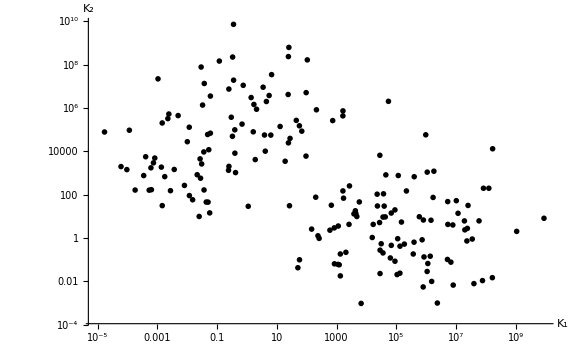

```mathematica
biPlot=ListLogLogPlot[Transpose[{biParK1,biParK2}],ImageSize->Large,PlotRange->Full,PlotLabel->None,LabelStyle->{32,GrayLevel[0]},AxesLabel->{"K_1","K_2"},Ticks->{Table[{10^(3 k),Superscript[10,3k]},{k,-2,3}], Table[{10^(3 k),Superscript[10,3k]},{k,-2,3}]},TicksStyle->Directive["Label", 14],AxesStyle-> Thick,PlotTheme->"Monochrome"]
```

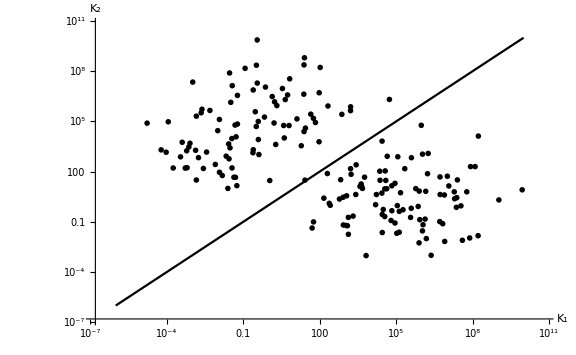

```mathematica
Show[LogLogPlot[x,{x,10^(-6),10^10},PlotRange->Full,ImageSize->Large,PlotTheme->"Monochrome",PlotLabel->None,LabelStyle->{32,GrayLevel[0]},AxesLabel->{"K_1","K_2"},Ticks->{Table[{10^(3 k),Superscript[10,3k]},{k,-2,3}], Table[{10^(3 k),Superscript[10,3k]},{k,-2,3}]},TicksStyle->Directive["Label", 14],AxesStyle-> Thick],biPlot]
```

```mathematica
Length[bistableKs]
```

14502

```mathematica
transposedKs=Transpose[bistableKs];parK1=(transposedKs[[1]]*transposedKs[[10]])/(transposedKs[[2]]*transposedKs[[11]]);parK2=(transposedKs[[4]]*transposedKs[[8]])/(transposedKs[[5]]*transposedKs[[9]]);
```

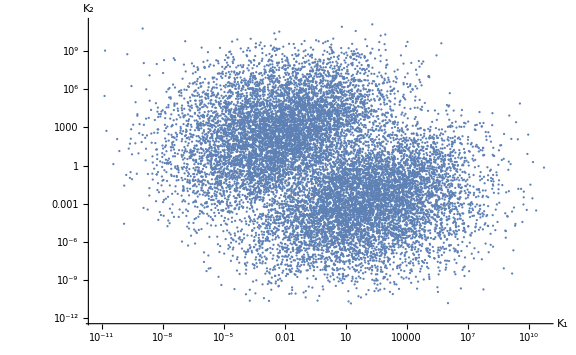

```mathematica
plot=ListLogLogPlot[Transpose[{parK1,parK2}],AxesLabel->{"K_1","K_2"},ImageSize->Large,PlotRange->Full,LabelStyle->{32,GrayLevel[0]},AxesStyle-> Thick,Ticks->Automatic,TicksStyle->Directive["Label", 20]]
```

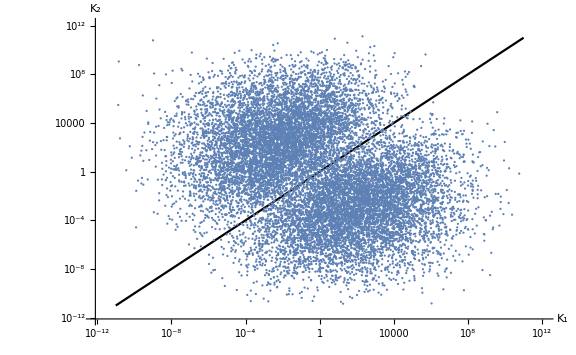

```mathematica
Show[LogLogPlot[x,{x,10^(-11),10^11},PlotRange->Full,ImageSize->Large,PlotLabel->None,LabelStyle->{32,GrayLevel[0]},AxesLabel->{"K_1","K_2"},Ticks->Automatic(*{Table[{10^(3 k),Superscript[10,3k]},{k,-2,3}], Table[{10^(3 k),Superscript[10,3k]},{k,-2,3}]}*),TicksStyle->Directive["Label", 14],AxesStyle-> Thick,PlotTheme->"Monochrome"],plot]
```